# (Top Project - dim6 ( Ctw,Cbw,CHud ,C3phiq ) and dim 8 ( C1quWH3 , C1qdWH3 , C2q2H4D , C3 q2H4D ,CudH4D ) - Left Handed Decay width - SM , dim 6 interference )

```mathematica
Quit[]
```

```mathematica
(* Activate FA/FC *)
$LoadFeynArts=True;
$FeynCalcStartupMessages=True;
<<FeynCalc`
$FAVerbose=0;
FAPatch[PatchModelsOnly->True];
```

FeynCalc 10.1.0 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynArts 3.12 (24 May 2024) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

Successfully patched FeynArts.

```mathematica
FAPatch[PatchModelsOnly->True,FAModelsDirectory->"/home/user1/Desktop/0000/FEYNCALC/Dim8New/LFullOperator6+8/LAll6and8twb/LFullOperatorAll"];
```

Successfully patched FeynArts.

```mathematica
(* Load FR model *)
InitializeModel["/home/user1/Desktop/0000/FEYNCALC/Dim8New/LFullOperator6+8/LAll6and8twb/LFullOperatorAll/LFullOperatorAll",GenericModel->"/home/user1/Desktop/0000/FEYNCALC/Dim8New/LFullOperator6+8/LAll6and8twb/LFullOperatorAll/LFullOperatorAll"]
```

True

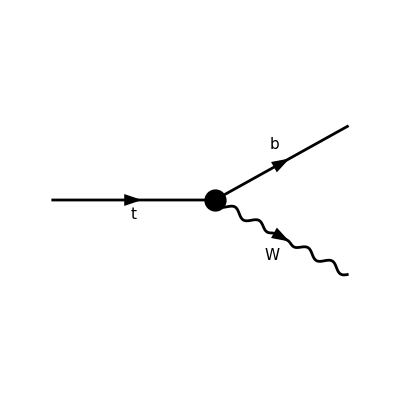

FeynArtsGraphics()(([] | Null | Null | Null | Null | Null))

```mathematica
(* Create diagrams *)
topo=CreateTopologies[0,1->2] (* # of loops = 0 *);

diag=InsertFields[topo,{F[9]}->{F[12], V[3]},InsertionLevel->{Particles},Model->"/home/user1/Desktop/0000/FEYNCALC/Dim8New/LFullOperator6+8/LAll6and8twb/LFullOperatorAll/LFullOperatorAll",GenericModel->"/home/user1/Desktop/0000/FEYNCALC/Dim8New/LFullOperator6+8/LAll6and8twb/LFullOperatorAll/LFullOperatorAll"];
Paint[diag,ColumnsXRows->{6,1},Numbering->None,SheetHeader->False,ImageSize->{800,200}]
```

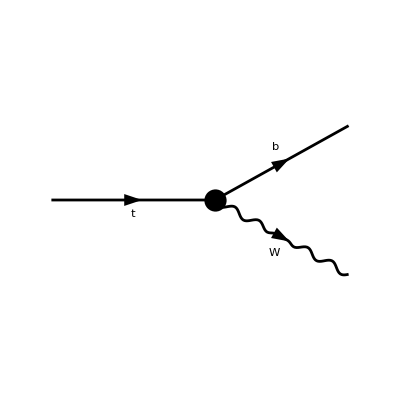

FeynArtsGraphics()(([]))

```mathematica
(* Diagram List *)
NofDiagrams=1;
lsD=Table[diag//DiagramDelete[#,Table[If[j≠i,j],{j,1,NofDiagrams}]/.Null->Sequence[]]&,{i,1,NofDiagrams}];
Paint[lsD[[1]],ColumnsXRows->{1,1},Numbering->None,SheetHeader->False,ImageSize->{200,100}]
```

```mathematica
(* Calculate amplitude *)
lsA0=Table[
FCFAConvert[CreateFeynAmp[lsD[[i]]],IncomingMomenta->{pt},OutgoingMomenta->{pb,pW},ChangeDimension->4,List->False,SMP->False,Contract->True,DropSumOver->True],
{i,1,NofDiagrams}];

lsA0=lsA0[[1]]//FeynAmpDenominatorExplicit//Simplify
(*%//TraditionalForm*)
```

-ⅈ (φ(OverBar[pb],FCGV(MB))).1/(2 Lambda^4)ⅈ δ_Col1Col2 (-vev ((γ̄·OverBar[pW]).(γ̄·(ε̄)^*(pW)).(γ̄)^7-(γ̄·(ε̄)^*(pW)).(γ̄·OverBar[pW]).(γ̄)^7) (vev^2 Conjugate[C1qdWH3]+2 Lambda^4 Conjugate[CbW])-vev Conjugate[CKM3x3] (C1quWH3 vev^2+2 CtW Lambda^2) ((γ̄·OverBar[pW]).(γ̄·(ε̄)^*(pW)).(γ̄)^6-(γ̄·(ε̄)^*(pW)).(γ̄·OverBar[pW]).(γ̄)^6)+2 gc145L Lambda^4 (γ̄·(ε̄)^*(pW)).(γ̄)^7+2 gc145R Lambda^4 (γ̄·(ε̄)^*(pW)).(γ̄)^6).(φ(OverBar[pt],FCGV(MT)))

```mathematica
gc145L = (FCGV["EL"]*(4*Lambda^4 + 2*C2q2H4D*vev^4 + C3q2H4D*vev^4 + 2*vev^4*Conjugate[C2q2H4D] + 4*Lambda^2*vev^2*Conjugate[C3phiq] - vev^4*Conjugate[C3q2H4D])*Conjugate[CKM3x3])/(4*Sqrt[2]*Lambda^4*sw);
gc145R = (FCGV["EL"]*(Lambda^4*vev^2*Conjugate[CHud] + vev^4*Conjugate[CudH4D]))/(2*Sqrt[2]*Lambda^4*sw);
sw=e/g;
```

```mathematica
lsA0//FullSimplify
```

-ⅈ (φ(OverBar[pb],FCGV(MB))).1/(8 e Lambda^4)ⅈ δ_Col1Col2 (-4 e vev ((γ̄·OverBar[pW]).(γ̄·(ε̄)^*(pW)).(γ̄)^7-(γ̄·(ε̄)^*(pW)).(γ̄·OverBar[pW]).(γ̄)^7) (vev^2 Conjugate[C1qdWH3]+2 Lambda^4 Conjugate[CbW])-4 e vev Conjugate[CKM3x3] (C1quWH3 vev^2+2 CtW Lambda^2) ((γ̄·OverBar[pW]).(γ̄·(ε̄)^*(pW)).(γ̄)^6-(γ̄·(ε̄)^*(pW)).(γ̄·OverBar[pW]).(γ̄)^6)+2 √2 g Conjugate[CKM3x3] FCGV(EL) (γ̄·(ε̄)^*(pW)).(γ̄)^7 (vev^4 (Conjugate[C2q2H4D]+C2q2H4D-Re(C3q2H4D)+C3q2H4D)+2 Lambda^2 vev^2 Conjugate[C3phiq]+2 Lambda^4)+2 √2 g vev^2 FCGV(EL) (γ̄·(ε̄)^*(pW)).(γ̄)^6 (Lambda^4 Conjugate[CHud]+vev^2 Conjugate[CudH4D])).(φ(OverBar[pt],FCGV(MT)))

```mathematica
(* Simplify *)
(* Setup the kinematics *)
SetMandelstam[s,t,u,pt,pb,pW,mpt,mpb,mpW];

rep0={EL->e,CW->cW,SW->sW,MW->mW,ME->0,MB->mb,MT->mt,
Pair[Momentum[pt],Momentum[pt]]->mt^2,
Pair[Momentum[pb],Momentum[pb]]->mb^2,
Pair[Momentum[pW],Momentum[pW]]->mW^2};
lsA=(lsA0//ReplaceAll@{FCGV[x_String]:>ToExpression[x]}(*//DiracSimplify*))/.rep0
```

-ⅈ (φ(OverBar[pb],mb)).1/(2 Lambda^4)ⅈ δ_Col1Col2 (-vev ((γ̄·OverBar[pW]).(γ̄·(ε̄)^*(pW)).(γ̄)^7-(γ̄·(ε̄)^*(pW)).(γ̄·OverBar[pW]).(γ̄)^7) (vev^2 Conjugate[C1qdWH3]+2 Lambda^4 Conjugate[CbW])-vev Conjugate[CKM3x3] (C1quWH3 vev^2+2 CtW Lambda^2) ((γ̄·OverBar[pW]).(γ̄·(ε̄)^*(pW)).(γ̄)^6-(γ̄·(ε̄)^*(pW)).(γ̄·OverBar[pW]).(γ̄)^6)+(g Conjugate[CKM3x3] (γ̄·(ε̄)^*(pW)).(γ̄)^7 (2 vev^4 Conjugate[C2q2H4D]+2 C2q2H4D vev^4+4 Lambda^2 vev^2 Conjugate[C3phiq]-vev^4 Conjugate[C3q2H4D]+C3q2H4D vev^4+4 Lambda^4))/(2 √2)+(g (γ̄·(ε̄)^*(pW)).(γ̄)^6 (Lambda^4 vev^2 Conjugate[CHud]+vev^4 Conjugate[CudH4D]))/(√2)).(φ(OverBar[pt],mt))

```mathematica
Fspin[x_]:=x//SUNFDeltaContract//FermionSpinSum[#,ExtraFactor->1/2]&//ReplaceAll[#,DiracTrace->TR]&
(lsAsq=(lsA*ComplexConjugate[lsA])//Simplify//Fspin//Contract)
```

```mathematica
lsAsqq=lsAsq/.{SUNN->Nc}//FullSimplify
```

1/(32 Lambda^8)Nc (4 g^2 vev^4 (Conjugate[CHud])^2 (ⅈ (ϵ̄)^(OverBar[pb]OverBar[pt](ε̄)^*(pW)ε̄(pW))+(OverBar[pb]·ε̄(pW)) (OverBar[pt]·(ε̄)^*(pW))+(OverBar[pb]·(ε̄)^*(pW)) (OverBar[pt]·ε̄(pW))-(OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW))) Lambda^8+8 g vev^2 Conjugate[CHud] (g Conjugate[CudH4D] (ⅈ (ϵ̄)^(OverBar[pb]OverBar[pt](ε̄)^*(pW)ε̄(pW))+(OverBar[pb]·ε̄(pW)) (OverBar[pt]·(ε̄)^*(pW))+(OverBar[pb]·(ε̄)^*(pW)) (OverBar[pt]·ε̄(pW))-(OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW))) vev^4+√2 mt (2 Conjugate[CbW] Lambda^4+vev^2 Conjugate[C1qdWH3]) (2 ⅈ (ϵ̄)^(OverBar[pb]OverBar[pW](ε̄)^*(pW)ε̄(pW))+(OverBar[pb]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW))+(OverBar[pb]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))-2 (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW))) vev+mb Conjugate[CKM3x3] (ⅈ √2 vev (2 CtW Lambda^2+C1quWH3 vev^2) (2 (ϵ̄)^(OverBar[pt]OverBar[pW](ε̄)^*(pW)ε̄(pW))+ⅈ ((OverBar[pt]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW))+(OverBar[pt]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))))+((ε̄)^*(pW)·ε̄(pW)) (2 g Lambda^2 mt Conjugate[C3phiq] vev^2+2 √2 (2 CtW Lambda^2+C1quWH3 vev^2) (OverBar[pt]·OverBar[pW]) vev+g mt (2 Lambda^4+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D)))))) Lambda^4+4 (g^2 (Conjugate[CudH4D])^2 (ⅈ (ϵ̄)^(OverBar[pb]OverBar[pt](ε̄)^*(pW)ε̄(pW))+(OverBar[pb]·ε̄(pW)) (OverBar[pt]·(ε̄)^*(pW))+(OverBar[pb]·(ε̄)^*(pW)) (OverBar[pt]·ε̄(pW))-(OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW))) vev^8+2 √2 g mt (2 Conjugate[CbW] Lambda^4+vev^2 Conjugate[C1qdWH3]) Conjugate[CudH4D] (2 ⅈ (ϵ̄)^(OverBar[pb]OverBar[pW](ε̄)^*(pW)ε̄(pW))+(OverBar[pb]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW))+(OverBar[pb]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))-2 (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW))) vev^5+8 (2 vev Conjugate[CbW] Lambda^4+vev^3 Conjugate[C1qdWH3])^2 (2 ⅈ (ϵ̄)^(OverBar[pb]OverBar[pW](ε̄)^*(pW)ε̄(pW)) (OverBar[pt]·OverBar[pW])+(OverBar[pb]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW)) (OverBar[pt]·OverBar[pW])+(OverBar[pb]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW)) (OverBar[pt]·OverBar[pW])+(OverBar[pb]·OverBar[pW]) (OverBar[pt]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW))+(OverBar[pb]·OverBar[pW]) (OverBar[pt]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))-(OverBar[pb]·OverBar[pt]) (OverBar[pW]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))-ⅈ (((ϵ̄)^(OverBar[pb]OverBar[pt](ε̄)^*(pW)ε̄(pW))-ⅈ ((OverBar[pb]·ε̄(pW)) (OverBar[pt]·(ε̄)^*(pW))+(OverBar[pb]·(ε̄)^*(pW)) (OverBar[pt]·ε̄(pW)))) OverBar[pW]^2-(ϵ̄)^(OverBar[pb]OverBar[pt]OverBar[pW]ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW))+(ϵ̄)^(OverBar[pb]OverBar[pt]OverBar[pW](ε̄)^*(pW)) (OverBar[pW]·ε̄(pW)))+((OverBar[pb]·OverBar[pt]) OverBar[pW]^2-2 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·OverBar[pW])) ((ε̄)^*(pW)·ε̄(pW))))+4 mb vev Conjugate[CKM3x3] (4 Conjugate[CbW] (-8 mt vev (2 CtW Lambda^2+C1quWH3 vev^2) ((OverBar[pW]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))-OverBar[pW]^2 ((ε̄)^*(pW)·ε̄(pW)))-2 ⅈ √2 g (ϵ̄)^(OverBar[pt]OverBar[pW](ε̄)^*(pW)ε̄(pW)) (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D)))-√2 g (OverBar[pt]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW)) (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D)))-√2 g ((OverBar[pt]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))-2 (OverBar[pt]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW))) (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D)))) Lambda^4+2 g vev^3 Conjugate[CudH4D] (ⅈ √2 vev (2 CtW Lambda^2+C1quWH3 vev^2) (2 (ϵ̄)^(OverBar[pt]OverBar[pW](ε̄)^*(pW)ε̄(pW))+ⅈ ((OverBar[pt]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW))+(OverBar[pt]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))))+((ε̄)^*(pW)·ε̄(pW)) (2 g Lambda^2 mt Conjugate[C3phiq] vev^2+2 √2 (2 CtW Lambda^2+C1quWH3 vev^2) (OverBar[pt]·OverBar[pW]) vev+g mt (2 Lambda^4+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D)))))+vev^2 Conjugate[C1qdWH3] (-16 mt vev (2 CtW Lambda^2+C1quWH3 vev^2) ((OverBar[pW]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))-OverBar[pW]^2 ((ε̄)^*(pW)·ε̄(pW)))-4 ⅈ √2 g (ϵ̄)^(OverBar[pt]OverBar[pW](ε̄)^*(pW)ε̄(pW)) (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D)))-2 √2 g ((OverBar[pt]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))-2 (OverBar[pt]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW))) (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D)))-2 √2 g (OverBar[pt]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW)) (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D)))))+(Conjugate[CKM3x3])^2 (-16 g^2 (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^8-32 g^2 vev^2 Conjugate[C3phiq] (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^6-64 √2 CtW g mt vev (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^6-128 ⅈ CtW^2 vev^2 (ϵ̄)^(OverBar[pb]OverBar[pt]OverBar[pW]ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW)) Lambda^4+128 CtW^2 vev^2 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW)) Lambda^4+128 ⅈ CtW^2 vev^2 (ϵ̄)^(OverBar[pb]OverBar[pt]OverBar[pW](ε̄)^*(pW)) (OverBar[pW]·ε̄(pW)) Lambda^4+128 CtW^2 vev^2 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW)) Lambda^4-128 CtW^2 vev^2 (OverBar[pb]·OverBar[pt]) (OverBar[pW]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW)) Lambda^4-16 g^2 vev^4 (Conjugate[C3phiq])^2 (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^4-16 ⅈ g^2 vev^4 Im(C3q2H4D) (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^4-32 √2 C1quWH3 g mt vev^3 (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^4-64 √2 CtW g mt vev^3 Conjugate[C3phiq] (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^4-256 CtW^2 vev^2 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^4+128 CtW^2 vev^2 (OverBar[pb]·OverBar[pt]) OverBar[pW]^2 ((ε̄)^*(pW)·ε̄(pW)) Lambda^4-32 g^2 vev^4 (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Re(C2q2H4D) Lambda^4-128 ⅈ C1quWH3 CtW vev^4 (ϵ̄)^(OverBar[pb]OverBar[pt]OverBar[pW]ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW)) Lambda^2+128 C1quWH3 CtW vev^4 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW)) Lambda^2+128 ⅈ C1quWH3 CtW vev^4 (ϵ̄)^(OverBar[pb]OverBar[pt]OverBar[pW](ε̄)^*(pW)) (OverBar[pW]·ε̄(pW)) Lambda^2+128 C1quWH3 CtW vev^4 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW)) Lambda^2-128 C1quWH3 CtW vev^4 (OverBar[pb]·OverBar[pt]) (OverBar[pW]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW)) Lambda^2-8 C3q2H4D g^2 vev^6 Conjugate[C3phiq] (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^2+8 g^2 vev^6 Conjugate[C3phiq] Conjugate[C3q2H4D] (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^2-32 √2 C3q2H4D CtW g mt vev^5 (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^2-32 √2 C1quWH3 g mt vev^5 Conjugate[C3phiq] (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^2-256 C1quWH3 CtW vev^4 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^2+128 C1quWH3 CtW vev^4 (OverBar[pb]·OverBar[pt]) OverBar[pW]^2 ((ε̄)^*(pW)·ε̄(pW)) Lambda^2-32 g^2 vev^6 Conjugate[C3phiq] (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Re(C2q2H4D) Lambda^2-64 √2 CtW g mt vev^5 (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW)) Re(C2q2H4D) Lambda^2+32 √2 CtW g mt vev^5 (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW)) Re(C3q2H4D) Lambda^2-32 ⅈ C1quWH3^2 vev^6 (ϵ̄)^(OverBar[pb]OverBar[pt]OverBar[pW]ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW))+32 C1quWH3^2 vev^6 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW))+32 ⅈ C1quWH3^2 vev^6 (ϵ̄)^(OverBar[pb]OverBar[pt]OverBar[pW](ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))+32 C1quWH3^2 vev^6 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))-32 C1quWH3^2 vev^6 (OverBar[pb]·OverBar[pt]) (OverBar[pW]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))+4 C2q2H4D^2 g^2 vev^8 (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW))-3 C3q2H4D^2 g^2 vev^8 (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW))-4 g^2 vev^8 (Conjugate[C2q2H4D])^2 (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW))-g^2 vev^8 (Conjugate[C3q2H4D])^2 (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW))-16 ⅈ √2 C1quWH3 g mt vev^7 Im(C3q2H4D) (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW))-64 C1quWH3^2 vev^6 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW))+32 C1quWH3^2 vev^6 (OverBar[pb]·OverBar[pt]) OverBar[pW]^2 ((ε̄)^*(pW)·ε̄(pW))-16 C2q2H4D g^2 vev^8 (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Re(C2q2H4D)-16 ⅈ g^2 vev^8 Im(C3q2H4D) (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Re(C2q2H4D)-32 √2 C1quWH3 g mt vev^7 (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW)) Re(C2q2H4D)-ⅈ (ϵ̄)^(OverBar[pb]OverBar[pt](ε̄)^*(pW)ε̄(pW)) (4 g^2 (Conjugate[C2q2H4D])^2 vev^8+8 g^2 Conjugate[C2q2H4D] (2 Conjugate[C3phiq] Lambda^2+C2q2H4D vev^2) vev^6+(g^2 (Conjugate[C3q2H4D])^2 vev^6-2 C3q2H4D g^2 Conjugate[C3q2H4D] vev^6+16 g^2 Lambda^4 (Conjugate[C3phiq])^2 vev^2+32 g^2 Lambda^4 Re(C2q2H4D) vev^2+16 ⅈ g^2 Im(C3q2H4D) (Lambda^4+vev^4 Re(C2q2H4D)) vev^2+16 g^2 Lambda^2 Conjugate[C3phiq] (2 Lambda^4+C2q2H4D vev^4+ⅈ vev^4 Im(C3q2H4D))-32 (2 CtW Lambda^2+C1quWH3 vev^2)^2 OverBar[pW]^2) vev^2+g^2 (16 Lambda^8+(4 C2q2H4D^2+C3q2H4D^2) vev^8))-16 ⅈ vev (2 CtW Lambda^2+C1quWH3 vev^2) (ϵ̄)^(OverBar[pb]OverBar[pW](ε̄)^*(pW)ε̄(pW)) (4 vev (2 CtW Lambda^2+C1quWH3 vev^2) (OverBar[pt]·OverBar[pW])+√2 g mt (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D))))+4 C3q2H4D g^2 vev^8 (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Re(C3q2H4D)+(OverBar[pb]·ε̄(pW)) ((OverBar[pt]·(ε̄)^*(pW)) (4 g^2 (Conjugate[C2q2H4D])^2 vev^8+8 g^2 Conjugate[C2q2H4D] (2 Conjugate[C3phiq] Lambda^2+C2q2H4D vev^2) vev^6+(g^2 (Conjugate[C3q2H4D])^2 vev^6-2 C3q2H4D g^2 Conjugate[C3q2H4D] vev^6+16 g^2 Lambda^4 (Conjugate[C3phiq])^2 vev^2+32 g^2 Lambda^4 Re(C2q2H4D) vev^2+16 ⅈ g^2 Im(C3q2H4D) (Lambda^4+vev^4 Re(C2q2H4D)) vev^2+16 g^2 Lambda^2 Conjugate[C3phiq] (2 Lambda^4+C2q2H4D vev^4+ⅈ vev^4 Im(C3q2H4D))-32 (2 CtW Lambda^2+C1quWH3 vev^2)^2 OverBar[pW]^2) vev^2+g^2 (16 Lambda^8+(4 C2q2H4D^2+C3q2H4D^2) vev^8))+8 vev (OverBar[pW]·(ε̄)^*(pW)) (4 vev (OverBar[pt]·OverBar[pW]) (2 CtW Lambda^2+C1quWH3 vev^2)^2+√2 g mt (4 CtW Lambda^6+2 C1quWH3 vev^2 Lambda^4+2 vev^2 (2 CtW Lambda^2+C1quWH3 vev^2) Conjugate[C3phiq] Lambda^2+C1quWH3 C3q2H4D vev^6+vev^4 (2 ⅈ CtW Im(C3q2H4D) Lambda^2+2 (2 CtW Lambda^2+C1quWH3 vev^2) Re(C2q2H4D)-C1quWH3 vev^2 Re(C3q2H4D)))))+(OverBar[pb]·(ε̄)^*(pW)) ((OverBar[pt]·ε̄(pW)) (4 g^2 (Conjugate[C2q2H4D])^2 vev^8+8 g^2 Conjugate[C2q2H4D] (2 Conjugate[C3phiq] Lambda^2+C2q2H4D vev^2) vev^6+(g^2 (Conjugate[C3q2H4D])^2 vev^6-2 C3q2H4D g^2 Conjugate[C3q2H4D] vev^6+16 g^2 Lambda^4 (Conjugate[C3phiq])^2 vev^2+32 g^2 Lambda^4 Re(C2q2H4D) vev^2+16 ⅈ g^2 Im(C3q2H4D) (Lambda^4+vev^4 Re(C2q2H4D)) vev^2+16 g^2 Lambda^2 Conjugate[C3phiq] (2 Lambda^4+C2q2H4D vev^4+ⅈ vev^4 Im(C3q2H4D))-32 (2 CtW Lambda^2+C1quWH3 vev^2)^2 OverBar[pW]^2) vev^2+g^2 (16 Lambda^8+(4 C2q2H4D^2+C3q2H4D^2) vev^8))+8 vev (OverBar[pW]·ε̄(pW)) (4 vev (OverBar[pt]·OverBar[pW]) (2 CtW Lambda^2+C1quWH3 vev^2)^2+√2 g mt (4 CtW Lambda^6+2 C1quWH3 vev^2 Lambda^4+2 vev^2 (2 CtW Lambda^2+C1quWH3 vev^2) Conjugate[C3phiq] Lambda^2+C1quWH3 C3q2H4D vev^6+vev^4 (2 ⅈ CtW Im(C3q2H4D) Lambda^2+2 (2 CtW Lambda^2+C1quWH3 vev^2) Re(C2q2H4D)-C1quWH3 vev^2 Re(C3q2H4D)))))))

```mathematica
1/(32 Lambda^8)Nc (4 g^2 vev^4 (Conjugate[CHud])^2 (ⅈ (ϵ̄)^(OverBar[pb] OverBar[pt] SuperStar[ε̄](pW)ε̄(pW))+(OverBar[pb]"·"ε̄(pW)) (OverBar[pt]"·"SuperStar[ε̄](pW))+(OverBar[pb]"·"SuperStar[ε̄](pW)) (OverBar[pt]"·"ε̄(pW))-(OverBar[pb]"·"OverBar[pt]) (SuperStar[ε̄](pW)"·"ε̄(pW))) Lambda^8+
```

```mathematica
1/(32 Lambda^8)*Nc*(4*g^2*vev^4*Conjugate[CHud]^2*(I*LeviCivitaContraction[Pb,pt,Epclh,Eplh]+MinkSP[Pb,Eplh]*MinkSP[pt,Epclh]+MinkSP[Pb,Epclh]*MinkSP[pt,Eplh]-MinkSP[Pb,pt]*MinkSP[Epclh,Eplh])*Lambda^8+
```

```mathematica
8 g vev^2 Conjugate[CHud] (g Conjugate[CudH4D] (ⅈ (ϵ̄)^(OverBar[pb] OverBar[pt] SuperStar[ε̄](pW)ε̄(pW))+(OverBar[pb]"·"ε̄(pW)) (OverBar[pt]"·"SuperStar[ε̄](pW))+(OverBar[pb]"·"SuperStar[ε̄](pW)) (OverBar[pt]"·"ε̄(pW))-(OverBar[pb]"·"OverBar[pt]) (SuperStar[ε̄](pW)"·"ε̄(pW))) vev^4+√2 mt (2 Conjugate[CbW] Lambda^4+vev^2 Conjugate[C1qdWH3]) (2 ⅈ (ϵ̄)^(OverBar[pb] OverBar[pW] SuperStar[ε̄](pW)ε̄(pW))+(OverBar[pb]"·"ε̄(pW)) (OverBar[pW]"·"SuperStar[ε̄](pW))+(OverBar[pb]"·"SuperStar[ε̄](pW)) (OverBar[pW]"·"ε̄(pW))-2 (OverBar[pb]"·"OverBar[pW]) (SuperStar[ε̄](pW)"·"ε̄(pW))) vev+
```

```mathematica
8*g*vev^2*Conjugate[CHud]*(g*Conjugate[CudH4D]*(I*LeviCivitaContraction[pb,pt,EpWStar,EpW]+MinkSP[pb,Eplh]*MinkSP[pt,Epclh]+MinkSP[pb,Epclh]*MinkSP[pt,Eplh]-MinkSP[pb,pt]*MinkSP[Epclh,Eplh])*vev^4+Sqrt[2]*mt*(2*Conjugate[CbW]*Lambda^4+vev^2*Conjugate[C1qdWH3])*(2*I*LeviCivitaContraction[pb,pW,Epclh,Eplh]+MinkSP[pb,Eplh]*MinkSP[pW,Epclh]+MinkSP[pb,Epclh]*MinkSP[pW,Eplh]-2*MinkSP[pb,pW]*MinkSP[Epclh,Eplh])*vev+
```

```mathematica
mb Conjugate[CKM3x3] (ⅈ √2 vev (2 CtW Lambda^2+C1quWH3 vev^2) (2 (ϵ̄)^(OverBar[pt] OverBar[pW] SuperStar[ε̄](pW)ε̄(pW))+ⅈ ((OverBar[pt]"·"ε̄(pW)) (OverBar[pW]"·"SuperStar[ε̄](pW))+(OverBar[pt]"·"SuperStar[ε̄](pW)) (OverBar[pW]"·"ε̄(pW))))+(SuperStar[ε̄](pW)"·"ε̄(pW)) (2 g Lambda^2 mt Conjugate[C3phiq] vev^2+2 √2 (2 CtW Lambda^2+C1quWH3 vev^2) (OverBar[pt]"·"OverBar[pW]) vev+g mt (2 Lambda^4+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D)))))) Lambda^4+
```

```mathematica
mb*Conjugate[CKM3x3]*(I*Sqrt[2]*vev*(2*CtW*Lambda^2+C1quWH3*vev^2)*(2*LeviCivitaContraction[pt,pW,Epclh,Eplh]+I*(MinkSP[pt,Eplh]*MinkSP[pW,Epclh]+MinkSP[pt,Epclh]*MinkSP[pW,Eplh]))+MinkSP[Epclh,Eplh]*(2*g*Lambda^2*mt*Conjugate[C3phiq]*vev^2+2*Sqrt[2]*(2*CtW*Lambda^2+C1quWH3*vev^2)*MinkSP[pt,pW]*vev+g*mt*(2*Lambda^4+C3q2H4D*vev^4+vev^4*(C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])))))*Lambda^4+
```

```mathematica
4 (g^2 (Conjugate[CudH4D])^2 (ⅈ (ϵ̄)^(OverBar[pb] OverBar[pt] SuperStar[ε̄](pW)ε̄(pW))+(OverBar[pb]"·"ε̄(pW)) (OverBar[pt]"·"SuperStar[ε̄](pW))+(OverBar[pb]"·"SuperStar[ε̄](pW)) (OverBar[pt]"·"ε̄(pW))-(OverBar[pb]"·"OverBar[pt]) (SuperStar[ε̄](pW)"·"ε̄(pW))) vev^8+2 √2 g mt (2 Conjugate[CbW] Lambda^4+vev^2 Conjugate[C1qdWH3]) Conjugate[CudH4D] (2 ⅈ (ϵ̄)^(OverBar[pb] OverBar[pW] SuperStar[ε̄](pW)ε̄(pW))+(OverBar[pb]"·"ε̄(pW)) (OverBar[pW]"·"SuperStar[ε̄](pW))+(OverBar[pb]"·"SuperStar[ε̄](pW)) (OverBar[pW]"·"ε̄(pW))-2 (OverBar[pb]"·"OverBar[pW]) (SuperStar[ε̄](pW)"·"ε̄(pW))) vev^5+
```

```mathematica
4*(g^2*Conjugate[CudH4D]^2*(I*LeviCivitaContraction[pb,pt,Epclh,Eplh]+MinkSP[pb,Eplh]*MinkSP[pt,Epclh]+MinkSP[pb,Epclh]*MinkSP[pt,Eplh]-MinkSP[pb,pt]*MinkSP[Epclh,Eplh])*vev^8+2*Sqrt[2]*g*mt*(2*Conjugate[CbW]*Lambda^4+vev^2*Conjugate[C1qdWH3])*Conjugate[CudH4D]*(2*I*LeviCivitaContraction[pb,pW,Epclh,Eplh]+MinkSP[pb,Eplh]*MinkSP[pW,Epclh]+MinkSP[pb,Epclh]*MinkSP[pW,Eplh]-2*MinkSP[pb,pW]*MinkSP[Epclh,Eplh])*vev^5+
```

```mathematica
8 (2 vev Conjugate[CbW] Lambda^4+vev^3 Conjugate[C1qdWH3])^2 (2 ⅈ (ϵ̄)^(OverBar[pb] OverBar[pW] SuperStar[ε̄](pW)ε̄(pW)) (OverBar[pt]"·"OverBar[pW])+(OverBar[pb]"·"ε̄(pW)) (OverBar[pW]"·"SuperStar[ε̄](pW)) (OverBar[pt]"·"OverBar[pW])+(OverBar[pb]"·"SuperStar[ε̄](pW)) (OverBar[pW]"·"ε̄(pW)) (OverBar[pt]"·"OverBar[pW])+(OverBar[pb]"·"OverBar[pW]) (OverBar[pt]"·"ε̄(pW)) (OverBar[pW]"·"SuperStar[ε̄](pW))+(OverBar[pb]"·"OverBar[pW]) (OverBar[pt]"·"SuperStar[ε̄](pW)) (OverBar[pW]"·"ε̄(pW))-(OverBar[pb]"·"OverBar[pt]) (OverBar[pW]"·"SuperStar[ε̄](pW)) (OverBar[pW]"·"ε̄(pW))-ⅈ (((ϵ̄)^(OverBar[pb] OverBar[pt] SuperStar[ε̄](pW)ε̄(pW))-ⅈ ((OverBar[pb]"·"ε̄(pW)) (OverBar[pt]"·"SuperStar[ε̄](pW))+(OverBar[pb]"·"SuperStar[ε̄](pW)) (OverBar[pt]"·"ε̄(pW)))) OverBar[pW]^2-(ϵ̄)^(OverBar[pb] OverBar[pt] OverBar[pW] ε̄(pW)) (OverBar[pW]"·"SuperStar[ε̄](pW))+(ϵ̄)^(OverBar[pb] OverBar[pt] OverBar[pW] SuperStar[ε̄](pW)) (OverBar[pW]"·"ε̄(pW)))+((OverBar[pb]"·"OverBar[pt]) OverBar[pW]^2-2 (OverBar[pb]"·"OverBar[pW]) (OverBar[pt]"·"OverBar[pW])) (SuperStar[ε̄](pW)"·"ε̄(pW))))+
```

```mathematica
8*(2*vev*Conjugate[CbW]*Lambda^4+vev^3*Conjugate[C1qdWH3])^2*(2*I*LeviCivitaContraction[pb,pW,Epclh,Eplh]*MinkSP[pt,pW]+MinkSP[pb,Eplh]*MinkSP[pW,Epclh]*MinkSP[pt,pW]+MinkSP[pb,Epclh]*MinkSP[pW,Eplh]*MinkSP[pt,pW]+MinkSP[pb,pW]*MinkSP[pt,Eplh]*MinkSP[pW,Epclh]+MinkSP[pb,pW]*MinkSP[pt,Epclh]*MinkSP[pW,Eplh]-MinkSP[pb,pt]*MinkSP[pW,Epclh]*MinkSP[pW,Eplh]
-I*((LeviCivitaContraction[pb,pt,Epclh,Eplh]-I*(MinkSP[pb,Eplh]*MinkSP[pt,Epclh]+MinkSP[pb,Epclh]*MinkSP[pt,Eplh]))*MinkSP[pW,pW]
-LeviCivitaContraction[pb,pt,pW,Eplh]*MinkSP[pW,Epclh]+LeviCivitaContraction[pb,pt,pW,Epclh]*MinkSP[pW,Eplh])
+(MinkSP[pb,pt]*MinkSP[pW,pW]-2*MinkSP[pb,pW]*MinkSP[pt,pW])*MinkSP[Epclh,Eplh]))+
```

```mathematica
4 mb vev Conjugate[CKM3x3] (4 Conjugate[CbW] (-8 mt vev (2 CtW Lambda^2+C1quWH3 vev^2) ((OverBar[pW]"·"SuperStar[ε̄](pW)) (OverBar[pW]"·"ε̄(pW))-OverBar[pW]^2 (SuperStar[ε̄](pW)"·"ε̄(pW)))-2 ⅈ √2 g (ϵ̄)^(OverBar[pt] OverBar[pW] SuperStar[ε̄](pW)ε̄(pW)) (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D)))-√2 g (OverBar[pt]"·"ε̄(pW)) (OverBar[pW]"·"SuperStar[ε̄](pW)) (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D)))-√2 g ((OverBar[pt]"·"SuperStar[ε̄](pW)) (OverBar[pW]"·"ε̄(pW))-2 (OverBar[pt]"·"OverBar[pW]) (SuperStar[ε̄](pW)"·"ε̄(pW))) (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D)))) Lambda^4+
```

```mathematica
4*mb*vev*Conjugate[CKM3x3]*(4*Conjugate[CbW]*(-8*mt*vev*(2*CtW*Lambda^2+C1quWH3*vev^2)*(MinkSP[pW,Epclh]*MinkSP[pW,Eplh]-MinkSP[pW,pW]*MinkSP[Epclh,Eplh])-2*I*Sqrt[2]*g*LeviCivitaContraction[pt,pW,Epclh,Eplh]*(2*Lambda^4+2*vev^2*Conjugate[C3phiq]*Lambda^2+C3q2H4D*vev^4+vev^4*(C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))-Sqrt[2]*g*MinkSP[pt,Eplh]*MinkSP[pW,Epclh]*(2*Lambda^4+2*vev^2*Conjugate[C3phiq]*Lambda^2+C3q2H4D*vev^4+vev^4*(C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))-Sqrt[2]*g*(MinkSP[pt,Epclh]*MinkSP[pW,Eplh]-2*MinkSP[pt,pW]*MinkSP[Epclh,Eplh])*(2*Lambda^4+2*vev^2*Conjugate[C3phiq]*Lambda^2+C3q2H4D*vev^4+vev^4*(C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])))*Lambda^4+
```

```mathematica
2 g vev^3 Conjugate[CudH4D] (ⅈ √2 vev (2 CtW Lambda^2+C1quWH3 vev^2) (2 (ϵ̄)^(OverBar[pt] OverBar[pW] SuperStar[ε̄](pW)ε̄(pW))+ⅈ ((OverBar[pt]"·"ε̄(pW)) (OverBar[pW]"·"SuperStar[ε̄](pW))+(OverBar[pt]"·"SuperStar[ε̄](pW)) (OverBar[pW]"·"ε̄(pW))))+(SuperStar[ε̄](pW)"·"ε̄(pW)) (2 g Lambda^2 mt Conjugate[C3phiq] vev^2+2 √2 (2 CtW Lambda^2+C1quWH3 vev^2) (OverBar[pt]"·"OverBar[pW]) vev+g mt (2 Lambda^4+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D)))))+
```

```mathematica
2*g*vev^3*Conjugate[CudH4D]*(I*Sqrt[2]*vev*(2*CtW*Lambda^2+C1quWH3*vev^2)*(2*LeviCivitaContraction[pt,pW,Epclh,Eplh]+I*(MinkSP[pt,Eplh]*MinkSP[pW,Epclh]+MinkSP[pt,Epclh]*MinkSP[pW,Eplh]))+MinkSP[Epclh,Eplh]*(2*g*Lambda^2*mt*Conjugate[C3phiq]*vev^2+2*Sqrt[2]*(2*CtW*Lambda^2+C1quWH3*vev^2)*MinkSP[pt,pW]*vev+g*mt*(2*Lambda^4+C3q2H4D*vev^4+vev^4*(C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))))+
```

```mathematica
vev^2 Conjugate[C1qdWH3] (-16 mt vev (2 CtW Lambda^2+C1quWH3 vev^2) ((OverBar[pW]"·"SuperStar[ε̄](pW)) (OverBar[pW]"·"ε̄(pW))-OverBar[pW]^2 (SuperStar[ε̄](pW)"·"ε̄(pW)))-4 ⅈ √2 g (ϵ̄)^(OverBar[pt] OverBar[pW] SuperStar[ε̄](pW)ε̄(pW)) (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D)))-2 √2 g ((OverBar[pt]"·"SuperStar[ε̄](pW)) (OverBar[pW]"·"ε̄(pW))-2 (OverBar[pt]"·"OverBar[pW]) (SuperStar[ε̄](pW)"·"ε̄(pW))) (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D)))-2 √2 g (OverBar[pt]"·"ε̄(pW)) (OverBar[pW]"·"SuperStar[ε̄](pW)) (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D)))))+
```

```mathematica
vev^2*Conjugate[C1qdWH3]*(-16*mt*vev*(2*CtW*Lambda^2+C1quWH3*vev^2)*(MinkSP[pW,Epclh]*MinkSP[pW,Eplh]-MinkSP[pW,pW]*MinkSP[Epclh,Eplh])-4*I*Sqrt[2]*g*LeviCivitaContraction[pt,pW,Epclh,Eplh]*(2*Lambda^4+2*vev^2*Conjugate[C3phiq]*Lambda^2+C3q2H4D*vev^4+vev^4*(C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))-2*Sqrt[2]*g*(MinkSP[pt,Epclh]*MinkSP[pW,Eplh]-2*MinkSP[pt,pW]*MinkSP[Epclh,Eplh])*(2*Lambda^4+2*vev^2*Conjugate[C3phiq]*Lambda^2+C3q2H4D*vev^4+vev^4*(C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))-2*Sqrt[2]*g*MinkSP[pt,Eplh]*MinkSP[pW,Epclh]*(2*Lambda^4+2*vev^2*Conjugate[C3phiq]*Lambda^2+vev^4*(C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))))+
```

```mathematica
(Conjugate[CKM3x3])^2 (-16 g^2 (OverBar[pb]"·"OverBar[pt]) (SuperStar[ε̄](pW)"·"ε̄(pW)) Lambda^8-32 g^2 vev^2 Conjugate[C3phiq] (OverBar[pb]"·"OverBar[pt]) (SuperStar[ε̄](pW)"·"ε̄(pW)) Lambda^6-64 √2 CtW g mt vev (OverBar[pb]"·"OverBar[pW]) (SuperStar[ε̄](pW)"·"ε̄(pW)) Lambda^6-128 ⅈ CtW^2 vev^2 (ϵ̄)^(OverBar[pb] OverBar[pt] OverBar[pW] ε̄(pW)) (OverBar[pW]"·"SuperStar[ε̄](pW)) Lambda^4+128 CtW^2 vev^2 (OverBar[pb]"·"OverBar[pW]) (OverBar[pt]"·"ε̄(pW)) (OverBar[pW]"·"SuperStar[ε̄](pW)) Lambda^4+128 ⅈ CtW^2 vev^2 (ϵ̄)^(OverBar[pb] OverBar[pt] OverBar[pW] SuperStar[ε̄](pW)) (OverBar[pW]"·"ε̄(pW)) Lambda^4+128 CtW^2 vev^2 (OverBar[pb]"·"OverBar[pW]) (OverBar[pt]"·"SuperStar[ε̄](pW)) (OverBar[pW]"·"ε̄(pW)) Lambda^4-128 CtW^2 vev^2 (OverBar[pb]"·"OverBar[pt]) (OverBar[pW]"·"SuperStar[ε̄](pW)) (OverBar[pW]"·"ε̄(pW)) Lambda^4-16 g^2 vev^4 (Conjugate[C3phiq])^2 (OverBar[pb]"·"OverBar[pt]) (SuperStar[ε̄](pW)"·"ε̄(pW)) Lambda^4-16 ⅈ g^2 vev^4 Im(C3q2H4D) (OverBar[pb]"·"OverBar[pt]) (SuperStar[ε̄](pW)"·"ε̄(pW)) Lambda^4-
```

```mathematica
(Conjugate[CKM3x3])^2*(-16*g^2*MinkSP[pb,pt]*MinkSP[Epclh,Eplh]*Lambda^8-32*g^2*vev^2*Conjugate[C3phiq]*MinkSP[pb,pt]*MinkSP[Epclh,Eplh]*Lambda^6-64*Sqrt[2]*CtW*g*mt*vev*MinkSP[pb,pW]*MinkSP[Epclh,Eplh]*Lambda^6-128*I*CtW^2*vev^2*LeviCivitaContraction[pb,pt,pW,Eplh]*MinkSP[pW,Epclh]*Lambda^4+128*CtW^2*vev^2*MinkSP[pb,pW]*MinkSP[pt,Eplh]*MinkSP[pW,Epclh]*Lambda^4+128*I*CtW^2*vev^2*LeviCivitaContraction[pb,pt,pW,Epclh]*MinkSP[pW,Eplh]*Lambda^4+128*CtW^2*vev^2*MinkSP[pb,pW]*MinkSP[pt,Epclh]*MinkSP[pW,Eplh]*Lambda^4-128*CtW^2*vev^2*MinkSP[pb,pt]*MinkSP[pW,Epclh]*MinkSP[pW,Eplh]*Lambda^4-16*g^2*vev^4*Conjugate[C3phiq]^2*MinkSP[pb,pt]*MinkSP[Epclh,Eplh]*Lambda^4-16*I*g^2*vev^4*Im[C3q2H4D]*MinkSP[pb,pt]*MinkSP[Epclh,Eplh]*Lambda^4-
```

```mathematica
32 √2 C1quWH3 g mt vev^3 (OverBar[pb]"·"OverBar[pW]) (SuperStar[ε̄](pW)"·"ε̄(pW)) Lambda^4-64 √2 CtW g mt vev^3 Conjugate[C3phiq] (OverBar[pb]"·"OverBar[pW]) (SuperStar[ε̄](pW)"·"ε̄(pW)) Lambda^4-256 CtW^2 vev^2 (OverBar[pb]"·"OverBar[pW]) (OverBar[pt]"·"OverBar[pW]) (SuperStar[ε̄](pW)"·"ε̄(pW)) Lambda^4+128 CtW^2 vev^2 (OverBar[pb]"·"OverBar[pt]) OverBar[pW]^2 (SuperStar[ε̄](pW)"·"ε̄(pW)) Lambda^4-32 g^2 vev^4 (OverBar[pb]"·"OverBar[pt]) (SuperStar[ε̄](pW)"·"ε̄(pW)) Re(C2q2H4D) Lambda^4-128 ⅈ C1quWH3 CtW vev^4 (ϵ̄)^(OverBar[pb] OverBar[pt] OverBar[pW] ε̄(pW)) (OverBar[pW]"·"SuperStar[ε̄](pW)) Lambda^2+
```

```mathematica
32*Sqrt[2]*C1quWH3*g*mt*vev^3*MinkSP[pb,pW]*MinkSP[Epclh,Eplh]*Lambda^4-64*Sqrt[2]*CtW*g*mt*vev^3*Conjugate[C3phiq]*MinkSP[pb,pW]*MinkSP[Epclh,Eplh]*Lambda^4-256*CtW^2*vev^2*MinkSP[pb,pW]*MinkSP[pt,pW]*MinkSP[Epclh,Eplh]*Lambda^4+128*CtW^2*vev^2*MinkSP[pb,pt]*MinkSP[pW,pW]*MinkSP[Epclh,Eplh]*Lambda^4-32*g^2*vev^4*MinkSP[pb,pt]*MinkSP[Epclh,Eplh]*Re[C2q2H4D]*Lambda^4-128*I*C1quWH3*CtW*vev^4*LeviCivitaContraction[pb,pt,pW,Eplh]*MinkSP[pW,Epclh]*Lambda^2+
```

```mathematica
128 C1quWH3 CtW vev^4 (OverBar[pb]"·"OverBar[pW]) (OverBar[pt]"·"ε̄(pW)) (OverBar[pW]"·"SuperStar[ε̄](pW)) Lambda^2+128 ⅈ C1quWH3 CtW vev^4 (ϵ̄)^(OverBar[pb] OverBar[pt] OverBar[pW] SuperStar[ε̄](pW)) (OverBar[pW]"·"ε̄(pW)) Lambda^2+128 C1quWH3 CtW vev^4 (OverBar[pb]"·"OverBar[pW]) (OverBar[pt]"·"SuperStar[ε̄](pW)) (OverBar[pW]"·"ε̄(pW)) Lambda^2-128 C1quWH3 CtW vev^4 (OverBar[pb]"·"OverBar[pt]) (OverBar[pW]"·"SuperStar[ε̄](pW)) (OverBar[pW]"·"ε̄(pW)) Lambda^2-8 C3q2H4D g^2 vev^6 Conjugate[C3phiq] (OverBar[pb]"·"OverBar[pt]) (SuperStar[ε̄](pW)"·"ε̄(pW)) Lambda^2+8 g^2 vev^6 Conjugate[C3phiq] Conjugate[C3q2H4D] (OverBar[pb]"·"OverBar[pt]) (SuperStar[ε̄](pW)"·"ε̄(pW)) Lambda^2-
```

```mathematica
128*C1quWH3*CtW*vev^4*MinkSP[pb,pW]*MinkSP[pt,Eplh]*MinkSP[pW,Epclh]*Lambda^2+128*I*C1quWH3*CtW*vev^4*LeviCivitaContraction[pb,pt,pW,Epclh]*MinkSP[pW,Eplh]*Lambda^2+128*C1quWH3*CtW*vev^4*MinkSP[pb,pW]*MinkSP[pt,Epclh]*MinkSP[pW,Eplh]*Lambda^2-128*C1quWH3*CtW*vev^4*MinkSP[pb,pt]*MinkSP[pW,Epclh]*MinkSP[pW,Eplh]*Lambda^2-8*C3q2H4D*g^2*vev^6*Conjugate[C3phiq]*MinkSP[pb,pt]*MinkSP[Epclh,Eplh]*Lambda^2+8*g^2*vev^6*Conjugate[C3phiq]*Conjugate[C3q2H4D]*MinkSP[pb,pt]*MinkSP[Epclh,Eplh]*Lambda^2-
```

```mathematica
32 √2 C3q2H4D CtW g mt vev^5 (OverBar[pb]"·"OverBar[pW]) (SuperStar[ε̄](pW)"·"ε̄(pW)) Lambda^2-32 √2 C1quWH3 g mt vev^5 Conjugate[C3phiq] (OverBar[pb]"·"OverBar[pW]) (SuperStar[ε̄](pW)"·"ε̄(pW)) Lambda^2-256 C1quWH3 CtW vev^4 (OverBar[pb]"·"OverBar[pW]) (OverBar[pt]"·"OverBar[pW]) (SuperStar[ε̄](pW)"·"ε̄(pW)) Lambda^2+128 C1quWH3 CtW vev^4 (OverBar[pb]"·"OverBar[pt]) OverBar[pW]^2 (SuperStar[ε̄](pW)"·"ε̄(pW)) Lambda^2-32 g^2 vev^6 Conjugate[C3phiq] (OverBar[pb]"·"OverBar[pt]) (SuperStar[ε̄](pW)"·"ε̄(pW)) Re(C2q2H4D) Lambda^2-64 √2 CtW g mt vev^5 (OverBar[pb]"·"OverBar[pW]) (SuperStar[ε̄](pW)"·"ε̄(pW)) Re(C2q2H4D) Lambda^2+32 √2 CtW g mt vev^5 (OverBar[pb]"·"OverBar[pW]) (SuperStar[ε̄](pW)"·"ε̄(pW)) Re(C3q2H4D) Lambda^2-32 ⅈ C1quWH3^2 vev^6 (ϵ̄)^(OverBar[pb] OverBar[pt] OverBar[pW] ε̄(pW)) (OverBar[pW]"·"SuperStar[ε̄](pW))+
```

```mathematica
32 Sqrt[2]*C3q2H4D*CtW*g*mt*vev^5*MinkSP[pb,pW]*MinkSP[Epclh,Eplh]*Lambda^2-32 Sqrt[2]*C1quWH3*g*mt*vev^5*Conjugate[C3phiq]*MinkSP[pb,pW]*MinkSP[Epclh,Eplh]*Lambda^2-256*C1quWH3*CtW*vev^4*MinkSP[pb,pW]*MinkSP[pt,pW]*MinkSP[Epclh,Eplh]*Lambda^2+128*C1quWH3*CtW*vev^4*MinkSP[pb,pt]*MinkSP[pW,pW]*MinkSP[Epclh,Eplh]*Lambda^2-32*g^2*vev^6*Conjugate[C3phiq]*MinkSP[pb,pt]*MinkSP[Epclh,Eplh]*Re[C2q2H4D]*Lambda^2-64 Sqrt[2]*CtW*g*mt*vev^5*MinkSP[pb,pW]*MinkSP[Epclh,Eplh]*Re[C2q2H4D]*Lambda^2+32 Sqrt[2]*CtW*g*mt*vev^5*MinkSP[pb,pW]*MinkSP[Epclh,Eplh]*Re[C3q2H4D]*Lambda^2-32 I*C1quWH3^2*vev^6*LeviCivitaContraction[pb,pt,pW,Eplh]*MinkSP[pW,Epclh]+
```

```mathematica
32 C1quWH3^2 vev^6 (OverBar[pb]"·"OverBar[pW]) (OverBar[pt]"·"ε̄(pW)) (OverBar[pW]"·"SuperStar[ε̄](pW))+32 ⅈ C1quWH3^2 vev^6 (ϵ̄)^(OverBar[pb] OverBar[pt] OverBar[pW] SuperStar[ε̄](pW)) (OverBar[pW]"·"ε̄(pW))+32 C1quWH3^2 vev^6 (OverBar[pb]"·"OverBar[pW]) (OverBar[pt]"·"SuperStar[ε̄](pW)) (OverBar[pW]"·"ε̄(pW))-32 C1quWH3^2 vev^6 (OverBar[pb]"·"OverBar[pt]) (OverBar[pW]"·"SuperStar[ε̄](pW)) (OverBar[pW]"·"ε̄(pW))+4 C2q2H4D^2 g^2 vev^8 (OverBar[pb]"·"OverBar[pt]) (SuperStar[ε̄](pW)"·"ε̄(pW))-3 C3q2H4D^2 g^2 vev^8 (OverBar[pb]"·"OverBar[pt]) (SuperStar[ε̄](pW)"·"ε̄(pW))-4 g^2 vev^8 (Conjugate[C2q2H4D])^2 (OverBar[pb]"·"OverBar[pt]) (SuperStar[ε̄](pW)"·"ε̄(pW))-g^2 vev^8 (Conjugate[C3q2H4D])^2 (OverBar[pb]"·"OverBar[pt]) (SuperStar[ε̄](pW)"·"ε̄(pW))-
```

```mathematica
32*C1quWH3^2*vev^6*MinkSP[pb,pW]*MinkSP[pt,Eplh]*MinkSP[pW,Epclh]+32 I*C1quWH3^2*vev^6*LeviCivitaContraction[pb,pt,pW,Epclh]*MinkSP[pW,Eplh]+32*C1quWH3^2*vev^6*MinkSP[pb,pW]*MinkSP[pt,Epclh]*MinkSP[pW,Eplh]-32*C1quWH3^2*vev^6*MinkSP[pb,pt]*MinkSP[pW,Epclh]*MinkSP[pW,Eplh]+4*C2q2H4D^2*g^2*vev^8*MinkSP[pb,pt]*MinkSP[Epclh,Eplh]-3*C3q2H4D^2*g^2*vev^8*MinkSP[pb,pt]*MinkSP[Epclh,Eplh]-4*g^2*vev^8*Conjugate[C2q2H4D]^2*MinkSP[pb,pt]*MinkSP[Epclh,Eplh]-g^2*vev^8*Conjugate[C3q2H4D]^2*MinkSP[pb,pt]*MinkSP[Epclh,Eplh]-
```

```mathematica
16 ⅈ √2 C1quWH3 g mt vev^7 Im(C3q2H4D) (OverBar[pb]"·"OverBar[pW]) (SuperStar[ε̄](pW)"·"ε̄(pW))-64 C1quWH3^2 vev^6 (OverBar[pb]"·"OverBar[pW]) (OverBar[pt]"·"OverBar[pW]) (SuperStar[ε̄](pW)"·"ε̄(pW))+32 C1quWH3^2 vev^6 (OverBar[pb]"·"OverBar[pt]) OverBar[pW]^2 (SuperStar[ε̄](pW)"·"ε̄(pW))-16 C2q2H4D g^2 vev^8 (OverBar[pb]"·"OverBar[pt]) (SuperStar[ε̄](pW)"·"ε̄(pW)) Re(C2q2H4D)-16 ⅈ g^2 vev^8 Im(C3q2H4D) (OverBar[pb]"·"OverBar[pt]) (SuperStar[ε̄](pW)"·"ε̄(pW)) Re(C2q2H4D)-32 √2 C1quWH3 g mt vev^7 (OverBar[pb]"·"OverBar[pW]) (SuperStar[ε̄](pW)"·"ε̄(pW)) Re(C2q2H4D)-
```

```mathematica
16 I Sqrt[2]*C1quWH3*g*mt*vev^7*Im[C3q2H4D]*MinkSP[pb,pW]*MinkSP[Epclh,Eplh]-64*C1quWH3^2*vev^6*MinkSP[pb,pW]*MinkSP[pt,pW]*MinkSP[Epclh,Eplh]+32*C1quWH3^2*vev^6*MinkSP[pb,pt]*MinkSP[pW,pW]*MinkSP[Epclh,Eplh]-16*C2q2H4D*g^2*vev^8*MinkSP[pb,pt]*MinkSP[Epclh,Eplh]*Re[C2q2H4D]-16 I*g^2*vev^8*Im[C3q2H4D]*MinkSP[pb,pt]*MinkSP[Epclh,Eplh]*Re[C2q2H4D]-32 Sqrt[2]*C1quWH3*g*mt*vev^7*MinkSP[pb,pW]*MinkSP[Epclh,Eplh]*Re[C2q2H4D]-
```

```mathematica
ⅈ (ϵ̄)^(OverBar[pb] OverBar[pt] SuperStar[ε̄](pW)ε̄(pW)) (4 g^2 (Conjugate[C2q2H4D])^2 vev^8+8 g^2 Conjugate[C2q2H4D] (2 Conjugate[C3phiq] Lambda^2+C2q2H4D vev^2) vev^6+(g^2 (Conjugate[C3q2H4D])^2 vev^6-2 C3q2H4D g^2 Conjugate[C3q2H4D] vev^6+16 g^2 Lambda^4 (Conjugate[C3phiq])^2 vev^2+32 g^2 Lambda^4 Re(C2q2H4D) vev^2+16 ⅈ g^2 Im(C3q2H4D) (Lambda^4+vev^4 Re(C2q2H4D)) vev^2+16 g^2 Lambda^2 Conjugate[C3phiq] (2 Lambda^4+C2q2H4D vev^4+ⅈ vev^4 Im(C3q2H4D))-32 (2 CtW Lambda^2+C1quWH3 vev^2)^2 OverBar[pW]^2) vev^2+g^2 (16 Lambda^8+(4 C2q2H4D^2+C3q2H4D^2) vev^8))-
```

```mathematica
I*LeviCivitaContraction[pb,pt,Epclh,Eplh]*(4*g^2*(Conjugate[C2q2H4D])^2*vev^8+8*g^2*Conjugate[C2q2H4D] *(2*Conjugate[C3phiq] *Lambda^2+C2q2H4D*vev^2)*vev^6+(g^2*(Conjugate[C3q2H4D])^2*vev^6-2*C3q2H4D*g^2*Conjugate[C3q2H4D] *vev^6+16*g^2*Lambda^4*(Conjugate[C3phiq])^2*vev^2+32*g^2*Lambda^4*Re[C2q2H4D]*vev^2+16 I*g^2*Im[C3q2H4D]*(Lambda^4+vev^4*Re[C2q2H4D])*vev^2+16*g^2*Lambda^2*Conjugate[C3phiq] *(2*Lambda^4+C2q2H4D*vev^4+I*vev^4*Im[C3q2H4D])-32*(2*CtW*Lambda^2+C1quWH3*vev^2)^2*MinkSP[pW,pW])*vev^2+g^2*(16*Lambda^8+(4*C2q2H4D^2+C3q2H4D^2)*vev^8))-
```

```mathematica
16 ⅈ vev (2 CtW Lambda^2+C1quWH3 vev^2) (ϵ̄)^(OverBar[pb] OverBar[pW] SuperStar[ε̄](pW)ε̄(pW)) (4 vev (2 CtW Lambda^2+C1quWH3 vev^2) (OverBar[pt]"·"OverBar[pW])+√2 g mt (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D))))+4 C3q2H4D g^2 vev^8 (OverBar[pb]"·"OverBar[pt]) (SuperStar[ε̄](pW)"·"ε̄(pW)) Re(C3q2H4D)+
```

```mathematica
16 I*vev*(2*CtW*Lambda^2+C1quWH3*vev^2)*LeviCivitaContraction[pb,pW,Epclh,Eplh]*(4*vev*(2*CtW*Lambda^2+C1quWH3*vev^2)*MinkSP[pt,pW]+Sqrt[2]*g*mt*(2*Lambda^4+2*vev^2*Conjugate[C3phiq] *Lambda^2+C3q2H4D*vev^4+vev^4*(C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])))
+4*C3q2H4D*g^2*vev^8*MinkSP[pb,pt]*MinkSP[Epclh,Eplh]*Re[C3q2H4D]+
```

```mathematica
(OverBar[pb]"·"ε̄(pW)) ((OverBar[pt]"·"SuperStar[ε̄](pW)) (4 g^2 (Conjugate[C2q2H4D])^2 vev^8+8 g^2 Conjugate[C2q2H4D] (2 Conjugate[C3phiq] Lambda^2+C2q2H4D vev^2) vev^6+(g^2 (Conjugate[C3q2H4D])^2 vev^6-2 C3q2H4D g^2 Conjugate[C3q2H4D] vev^6+16 g^2 Lambda^4 (Conjugate[C3phiq])^2 vev^2+32 g^2 Lambda^4 Re(C2q2H4D) vev^2+16 ⅈ g^2 Im(C3q2H4D) (Lambda^4+vev^4 Re(C2q2H4D)) vev^2+16 g^2 Lambda^2 Conjugate[C3phiq] (2 Lambda^4+C2q2H4D vev^4+ⅈ vev^4 Im(C3q2H4D))-32 (2 CtW Lambda^2+C1quWH3 vev^2)^2 OverBar[pW]^2) vev^2+g^2 (16 Lambda^8+(4 C2q2H4D^2+C3q2H4D^2) vev^8))+8 vev (OverBar[pW]"·"SuperStar[ε̄](pW)) (4 vev (OverBar[pt]"·"OverBar[pW]) (2 CtW Lambda^2+C1quWH3 vev^2)^2+√2 g mt (4 CtW Lambda^6+2 C1quWH3 vev^2 Lambda^4+2 vev^2 (2 CtW Lambda^2+C1quWH3 vev^2) Conjugate[C3phiq] Lambda^2+C1quWH3 C3q2H4D vev^6+vev^4 (2 ⅈ CtW Im(C3q2H4D) Lambda^2+2 (2 CtW Lambda^2+C1quWH3 vev^2) Re(C2q2H4D)-C1quWH3 vev^2 Re(C3q2H4D)))))+
```

```mathematica
MinkSP[pb,Eplh]*(MinkSP[pt,Epclh]*(4*g^2*Conjugate[C2q2H4D]^2*vev^8+8*g^2*Conjugate[C2q2H4D]*(2*Conjugate[C3phiq]*Lambda^2+C2q2H4D*vev^2)*vev^6+(g^2*Conjugate[C3q2H4D]^2*vev^6-2*C3q2H4D*g^2*Conjugate[C3q2H4D]*vev^6+16*g^2*Lambda^4*Conjugate[C3phiq]^2*vev^2+32*g^2*Lambda^4*Re[C2q2H4D]*vev^2+16 I*g^2*Im[C3q2H4D]*(Lambda^4+vev^4*Re[C2q2H4D])*vev^2+16*g^2*Lambda^2*Conjugate[C3phiq]*(2*Lambda^4+C2q2H4D*vev^4+I*vev^4*Im[C3q2H4D])-32*(2*CtW*Lambda^2+C1quWH3*vev^2)^2*MinkSP[pW,pW])*vev^2+g^2*(16*Lambda^8+(4*C2q2H4D^2+C3q2H4D^2)*vev^8))+8*vev*MinkSP[pW,Epclh]*(4*vev*MinkSP[pt,pW]*(2*CtW*Lambda^2+C1quWH3*vev^2)^2+Sqrt[2]*g*mt*(4*CtW*Lambda^6+2*C1quWH3*vev^2*Lambda^4+2*vev^2*(2*CtW*Lambda^2+C1quWH3*vev^2)*Conjugate[C3phiq]*Lambda^2+C1quWH3*C3q2H4D*vev^6+vev^4*(2 I*CtW*Im[C3q2H4D]*Lambda^2+2*(2*CtW*Lambda^2+C1quWH3*vev^2)*Re[C2q2H4D]-C1quWH3*vev^2*Re[C3q2H4D]))))+
```

```mathematica
(OverBar[pb]"·"SuperStar[ε̄](pW)) ((OverBar[pt]"·"ε̄(pW)) (4 g^2 (Conjugate[C2q2H4D])^2 vev^8+8 g^2 Conjugate[C2q2H4D] (2 Conjugate[C3phiq] Lambda^2+C2q2H4D vev^2) vev^6+(g^2 (Conjugate[C3q2H4D])^2 vev^6-2 C3q2H4D g^2 Conjugate[C3q2H4D] vev^6+16 g^2 Lambda^4 (Conjugate[C3phiq])^2 vev^2+32 g^2 Lambda^4 Re(C2q2H4D) vev^2+16 ⅈ g^2 Im(C3q2H4D) (Lambda^4+vev^4 Re(C2q2H4D)) vev^2+16 g^2 Lambda^2 Conjugate[C3phiq] (2 Lambda^4+C2q2H4D vev^4+ⅈ vev^4 Im(C3q2H4D))-32 (2 CtW Lambda^2+C1quWH3 vev^2)^2 OverBar[pW]^2) vev^2+g^2 (16 Lambda^8+(4 C2q2H4D^2+C3q2H4D^2) vev^8))+
```

```mathematica
MinkSP[pb,Epclh]*(MinkSP[pt,Eplh]*(4 g^2 Conjugate[C2q2H4D]^2 vev^8+8 g^2 Conjugate[C2q2H4D] (2 Conjugate[C3phiq] Lambda^2+C2q2H4D vev^2) vev^6+(g^2 Conjugate[C3q2H4D]^2 vev^6-2 C3q2H4D g^2 Conjugate[C3q2H4D] vev^6+16 g^2 Lambda^4 Conjugate[C3phiq]^2 vev^2+32 g^2 Lambda^4 Re[C2q2H4D] vev^2+16 I g^2 Im[C3q2H4D] (Lambda^4+vev^4 Re[C2q2H4D]) vev^2+16 g^2 Lambda^2 Conjugate[C3phiq] (2 Lambda^4+C2q2H4D vev^4+I vev^4 Im[C3q2H4D])-32 (2 CtW Lambda^2+C1quWH3 vev^2)^2MinkSP[pW,pW])vev^2+g^2 (16 Lambda^8+(4 C2q2H4D^2+C3q2H4D^2) vev^8))+
```

```mathematica
8 vev (OverBar[pW]"·"ε̄(pW)) (4 vev (OverBar[pt]"·"OverBar[pW]) (2 CtW Lambda^2+C1quWH3 vev^2)^2+√2 g mt (4 CtW Lambda^6+2 C1quWH3 vev^2 Lambda^4+2 vev^2 (2 CtW Lambda^2+C1quWH3 vev^2) Conjugate[C3phiq] Lambda^2+C1quWH3 C3q2H4D vev^6+vev^4 (2 ⅈ CtW Im(C3q2H4D) Lambda^2+2 (2 CtW Lambda^2+C1quWH3 vev^2) Re(C2q2H4D)-C1quWH3 vev^2 Re(C3q2H4D)))))))
```

```mathematica
8 vev MinkSP[pW,Eplh]*(4 vev MinkSP[pt,pW] (2 CtW Lambda^2+C1quWH3 vev^2)^2+Sqrt[2] g mt (4 CtW Lambda^6+2 C1quWH3 vev^2 Lambda^4+2 vev^2 (2 CtW Lambda^2+C1quWH3 vev^2) Conjugate[C3phiq]Lambda^2+C1quWH3 C3q2H4D vev^6+vev^4 (2 I CtW Im[C3q2H4D] Lambda^2+2 (2 CtW Lambda^2+C1quWH3 vev^2) Re[C2q2H4D]-C1quWH3 vev^2 Re[C3q2H4D]))))))
```

```mathematica
Quit[]
```

```mathematica
Pb={Eb,pb Sin[θ]Cos[ϕ],pb Sin[θ] Sin[ϕ],pb Cos[θ]};
pw={EW,-pb Sin[θ]Cos[ϕ],-pb Sin[θ] Sin[ϕ],-pb Cos[θ]};
pt={mt,0,0,0};
Eplh={0,1/Sqrt[2](Cos[θ]Cos[ϕ]-I Sin[ϕ]),1/Sqrt[2](Cos[θ] Sin[ϕ]+I Cos[ϕ]),1/Sqrt[2](-Sin[θ])};
Epclh={0,1/Sqrt[2](Cos[θ]Cos[ϕ]+I Sin[ϕ]),1/Sqrt[2](Cos[θ] Sin[ϕ]-I Cos[ϕ]),1/Sqrt[2](-Sin[θ])};
```

```mathematica
MinkSP[vec1_,vec2_]:=Times[vec1[[1]],vec2[[1]]]-Times[vec1[[2]],vec2[[2]]]-Times[vec1[[3]],vec2[[3]]]-Times[vec1[[4]],vec2[[4]]]
```

```mathematica
(*Define Levi-Civita with provided function, (-1)for lower index of Levi-Civita *)
LeviCivita[indices__]:=-Module[{list={indices}},If[Length[list]≠4||DuplicateFreeQ[list]===False,0,Signature[list]]]
(*Contraction of Levi-Civita with 4 specific 4-vectors*)
LeviCivitaContraction[Pb_,pt_,Epclh_,Eplh_]:=Sum[LeviCivita[mu,nu,rho,sigma]*Pb[[mu+1]] pt[[nu+1]] Epclh[[rho+1]]*Eplh[[sigma+1]],{mu,0,3},{nu,0,3},{rho,0,3},{sigma,0,3}]//Simplify
```

```mathematica
Msqt=1/(32 Lambda^8)*Nc*(4*g^2*vev^4*Conjugate[CHud]^2*(I*LeviCivitaContraction[Pb,pt,Epclh,Eplh]+MinkSP[Pb,Eplh]*MinkSP[pt,Epclh]+MinkSP[Pb,Epclh]*MinkSP[pt,Eplh]-MinkSP[Pb,pt]*MinkSP[Epclh,Eplh])*Lambda^8+8*g*vev^2*Conjugate[CHud]*(g*Conjugate[CudH4D]*(I*LeviCivitaContraction[Pb,pt,Epclh,Eplh]+MinkSP[Pb,Eplh]*MinkSP[pt,Epclh]+MinkSP[Pb,Epclh]*MinkSP[pt,Eplh]-MinkSP[Pb,pt]*MinkSP[Epclh,Eplh])*vev^4+Sqrt[2]*mt*(2*Conjugate[CbW]*Lambda^4+vev^2*Conjugate[C1qdWH3])*(2*I*LeviCivitaContraction[Pb,pw,Epclh,Eplh]+MinkSP[Pb,Eplh]*MinkSP[pw,Epclh]+MinkSP[Pb,Epclh]*MinkSP[pw,Eplh]-2*MinkSP[Pb,pw]*MinkSP[Epclh,Eplh])*vev+mb*Conjugate[CKM3x3]*(I*Sqrt[2]*vev*(2*CtW*Lambda^2+C1quWH3*vev^2)*(2*LeviCivitaContraction[pt,pw,Epclh,Eplh]+I*(MinkSP[pt,Eplh]*MinkSP[pw,Epclh]+MinkSP[pt,Epclh]*MinkSP[pw,Eplh]))+MinkSP[Epclh,Eplh]*(2*g*Lambda^2*mt*Conjugate[C3phiq]*vev^2+2*Sqrt[2]*(2*CtW*Lambda^2+C1quWH3*vev^2)*MinkSP[pt,pw]*vev+g*mt*(2*Lambda^4+C3q2H4D*vev^4+vev^4*(C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])))))*Lambda^4+4*(g^2*Conjugate[CudH4D]^2*(I*LeviCivitaContraction[Pb,pt,Epclh,Eplh]+MinkSP[Pb,Eplh]*MinkSP[pt,Epclh]+MinkSP[Pb,Epclh]*MinkSP[pt,Eplh]-MinkSP[Pb,pt]*MinkSP[Epclh,Eplh])*vev^8+2*Sqrt[2]*g*mt*(2*Conjugate[CbW]*Lambda^4+vev^2*Conjugate[C1qdWH3])*Conjugate[CudH4D]*(2*I*LeviCivitaContraction[Pb,pw,Epclh,Eplh]+MinkSP[Pb,Eplh]*MinkSP[pw,Epclh]+MinkSP[Pb,Epclh]*MinkSP[pw,Eplh]-2*MinkSP[Pb,pw]*MinkSP[Epclh,Eplh])*vev^5+8*(2*vev*Conjugate[CbW]*Lambda^4+vev^3*Conjugate[C1qdWH3])^2*(2*I*LeviCivitaContraction[Pb,pw,Epclh,Eplh]*MinkSP[pt,pw]+MinkSP[Pb,Eplh]*MinkSP[pw,Epclh]*MinkSP[pt,pw]+MinkSP[Pb,Epclh]*MinkSP[pw,Eplh]*MinkSP[pt,pw]+MinkSP[Pb,pw]*MinkSP[pt,Eplh]*MinkSP[pw,Epclh]+MinkSP[Pb,pw]*MinkSP[pt,Epclh]*MinkSP[pw,Eplh]-MinkSP[Pb,pt]*MinkSP[pw,Epclh]*MinkSP[pw,Eplh]
-I*((LeviCivitaContraction[Pb,pt,Epclh,Eplh]-I*(MinkSP[Pb,Eplh]*MinkSP[pt,Epclh]+MinkSP[Pb,Epclh]*MinkSP[pt,Eplh]))*MinkSP[pw,pw]
-LeviCivitaContraction[Pb,pt,pw,Eplh]*MinkSP[pw,Epclh]+LeviCivitaContraction[Pb,pt,pw,Epclh]*MinkSP[pw,Eplh])
+(MinkSP[Pb,pt]*MinkSP[pw,pw]-2*MinkSP[Pb,pw]*MinkSP[pt,pw])*MinkSP[Epclh,Eplh]))+4*mb*vev*Conjugate[CKM3x3]*(4*Conjugate[CbW]*(-8*mt*vev*(2*CtW*Lambda^2+C1quWH3*vev^2)*(MinkSP[pw,Epclh]*MinkSP[pw,Eplh]-MinkSP[pw,pw]*MinkSP[Epclh,Eplh])-2*I*Sqrt[2]*g*LeviCivitaContraction[pt,pw,Epclh,Eplh]*(2*Lambda^4+2*vev^2*Conjugate[C3phiq]*Lambda^2+C3q2H4D*vev^4+vev^4*(C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))-Sqrt[2]*g*MinkSP[pt,Eplh]*MinkSP[pw,Epclh]*(2*Lambda^4+2*vev^2*Conjugate[C3phiq]*Lambda^2+C3q2H4D*vev^4+vev^4*(C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))-Sqrt[2]*g*(MinkSP[pt,Epclh]*MinkSP[pw,Eplh]-2*MinkSP[pt,pw]*MinkSP[Epclh,Eplh])*(2*Lambda^4+2*vev^2*Conjugate[C3phiq]*Lambda^2+C3q2H4D*vev^4+vev^4*(C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])))*Lambda^4+2*g*vev^3*Conjugate[CudH4D]*(I*Sqrt[2]*vev*(2*CtW*Lambda^2+C1quWH3*vev^2)*(2*LeviCivitaContraction[pt,pw,Epclh,Eplh]+I*(MinkSP[pt,Eplh]*MinkSP[pw,Epclh]+MinkSP[pt,Epclh]*MinkSP[pw,Eplh]))+MinkSP[Epclh,Eplh]*(2*g*Lambda^2*mt*Conjugate[C3phiq]*vev^2+2*Sqrt[2]*(2*CtW*Lambda^2+C1quWH3*vev^2)*MinkSP[pt,pw]*vev+g*mt*(2*Lambda^4+C3q2H4D*vev^4+vev^4*(C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))))+vev^2*Conjugate[C1qdWH3]*(-16*mt*vev*(2*CtW*Lambda^2+C1quWH3*vev^2)*(MinkSP[pw,Epclh]*MinkSP[pw,Eplh]-MinkSP[pw,pw]*MinkSP[Epclh,Eplh])-4*I*Sqrt[2]*g*LeviCivitaContraction[pt,pw,Epclh,Eplh]*(2*Lambda^4+2*vev^2*Conjugate[C3phiq]*Lambda^2+C3q2H4D*vev^4+vev^4*(C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))-2*Sqrt[2]*g*(MinkSP[pt,Epclh]*MinkSP[pw,Eplh]-2*MinkSP[pt,pw]*MinkSP[Epclh,Eplh])*(2*Lambda^4+2*vev^2*Conjugate[C3phiq]*Lambda^2+C3q2H4D*vev^4+vev^4*(C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))-2*Sqrt[2]*g*MinkSP[pt,Eplh]*MinkSP[pw,Epclh]*(2*Lambda^4+2*vev^2*Conjugate[C3phiq]*Lambda^2+vev^4*(C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))))+(Conjugate[CKM3x3])^2*(-16*g^2*MinkSP[Pb,pt]*MinkSP[Epclh,Eplh]*Lambda^8-32*g^2*vev^2*Conjugate[C3phiq]*MinkSP[Pb,pt]*MinkSP[Epclh,Eplh]*Lambda^6-64*Sqrt[2]*CtW*g*mt*vev*MinkSP[Pb,pw]*MinkSP[Epclh,Eplh]*Lambda^6-128*I*CtW^2*vev^2*LeviCivitaContraction[Pb,pt,pw,Eplh]*MinkSP[pw,Epclh]*Lambda^4+128*CtW^2*vev^2*MinkSP[Pb,pw]*MinkSP[pt,Eplh]*MinkSP[pw,Epclh]*Lambda^4+128*I*CtW^2*vev^2*LeviCivitaContraction[Pb,pt,pw,Epclh]*MinkSP[pw,Eplh]*Lambda^4+128*CtW^2*vev^2*MinkSP[Pb,pw]*MinkSP[pt,Epclh]*MinkSP[pw,Eplh]*Lambda^4-128*CtW^2*vev^2*MinkSP[Pb,pt]*MinkSP[pw,Epclh]*MinkSP[pw,Eplh]*Lambda^4-16*g^2*vev^4*Conjugate[C3phiq]^2*MinkSP[Pb,pt]*MinkSP[Epclh,Eplh]*Lambda^4-16*I*g^2*vev^4*Im[C3q2H4D]*MinkSP[Pb,pt]*MinkSP[Epclh,Eplh]*Lambda^4-32*Sqrt[2]*C1quWH3*g*mt*vev^3*MinkSP[Pb,pw]*MinkSP[Epclh,Eplh]*Lambda^4-64*Sqrt[2]*CtW*g*mt*vev^3*Conjugate[C3phiq]*MinkSP[Pb,pw]*MinkSP[Epclh,Eplh]*Lambda^4-256*CtW^2*vev^2*MinkSP[Pb,pw]*MinkSP[pt,pw]*MinkSP[Epclh,Eplh]*Lambda^4+128*CtW^2*vev^2*MinkSP[Pb,pt]*MinkSP[pw,pw]*MinkSP[Epclh,Eplh]*Lambda^4-32*g^2*vev^4*MinkSP[Pb,pt]*MinkSP[Epclh,Eplh]*Re[C2q2H4D]*Lambda^4-128*I*C1quWH3*CtW*vev^4*LeviCivitaContraction[Pb,pt,pw,Eplh]*MinkSP[pw,Epclh]*Lambda^2+128*C1quWH3*CtW*vev^4*MinkSP[Pb,pw]*MinkSP[pt,Eplh]*MinkSP[pw,Epclh]*Lambda^2+128*I*C1quWH3*CtW*vev^4*LeviCivitaContraction[Pb,pt,pw,Epclh]*MinkSP[pw,Eplh]*Lambda^2+128*C1quWH3*CtW*vev^4*MinkSP[Pb,pw]*MinkSP[pt,Epclh]*MinkSP[pw,Eplh]*Lambda^2-128*C1quWH3*CtW*vev^4*MinkSP[Pb,pt]*MinkSP[pw,Epclh]*MinkSP[pw,Eplh]*Lambda^2-8*C3q2H4D*g^2*vev^6*Conjugate[C3phiq]*MinkSP[Pb,pt]*MinkSP[Epclh,Eplh]*Lambda^2+8*g^2*vev^6*Conjugate[C3phiq]*Conjugate[C3q2H4D]*MinkSP[Pb,pt]*MinkSP[Epclh,Eplh]*Lambda^2-32 Sqrt[2]*C3q2H4D*CtW*g*mt*vev^5*MinkSP[Pb,pw]*MinkSP[Epclh,Eplh]*Lambda^2-32 Sqrt[2]*C1quWH3*g*mt*vev^5*Conjugate[C3phiq]*MinkSP[Pb,pw]*MinkSP[Epclh,Eplh]*Lambda^2-256*C1quWH3*CtW*vev^4*MinkSP[Pb,pw]*MinkSP[pt,pw]*MinkSP[Epclh,Eplh]*Lambda^2+128*C1quWH3*CtW*vev^4*MinkSP[Pb,pt]*MinkSP[pw,pw]*MinkSP[Epclh,Eplh]*Lambda^2-32*g^2*vev^6*Conjugate[C3phiq]*MinkSP[Pb,pt]*MinkSP[Epclh,Eplh]*Re[C2q2H4D]*Lambda^2-64 Sqrt[2]*CtW*g*mt*vev^5*MinkSP[Pb,pw]*MinkSP[Epclh,Eplh]*Re[C2q2H4D]*Lambda^2+32 Sqrt[2]*CtW*g*mt*vev^5*MinkSP[Pb,pw]*MinkSP[Epclh,Eplh]*Re[C3q2H4D]*Lambda^2-32 I*C1quWH3^2*vev^6*LeviCivitaContraction[Pb,pt,pw,Eplh]*MinkSP[pw,Epclh]+32*C1quWH3^2*vev^6*MinkSP[Pb,pw]*MinkSP[pt,Eplh]*MinkSP[pw,Epclh]+32 I*C1quWH3^2*vev^6*LeviCivitaContraction[Pb,pt,pw,Epclh]*MinkSP[pw,Eplh]+32*C1quWH3^2*vev^6*MinkSP[Pb,pw]*MinkSP[pt,Epclh]*MinkSP[pw,Eplh]-32*C1quWH3^2*vev^6*MinkSP[Pb,pt]*MinkSP[pw,Epclh]*MinkSP[pw,Eplh]+4*C2q2H4D^2*g^2*vev^8*MinkSP[Pb,pt]*MinkSP[Epclh,Eplh]-3*C3q2H4D^2*g^2*vev^8*MinkSP[Pb,pt]*MinkSP[Epclh,Eplh]-4*g^2*vev^8*Conjugate[C2q2H4D]^2*MinkSP[Pb,pt]*MinkSP[Epclh,Eplh]-g^2*vev^8*Conjugate[C3q2H4D]^2*MinkSP[Pb,pt]*MinkSP[Epclh,Eplh]-16 I Sqrt[2]*C1quWH3*g*mt*vev^7*Im[C3q2H4D]*MinkSP[Pb,pw]*MinkSP[Epclh,Eplh]-64*C1quWH3^2*vev^6*MinkSP[Pb,pw]*MinkSP[pt,pw]*MinkSP[Epclh,Eplh]+32*C1quWH3^2*vev^6*MinkSP[Pb,pt]*MinkSP[pw,pw]*MinkSP[Epclh,Eplh]-16*C2q2H4D*g^2*vev^8*MinkSP[Pb,pt]*MinkSP[Epclh,Eplh]*Re[C2q2H4D]-16 I*g^2*vev^8*Im[C3q2H4D]*MinkSP[Pb,pt]*MinkSP[Epclh,Eplh]*Re[C2q2H4D]-32 Sqrt[2]*C1quWH3*g*mt*vev^7*MinkSP[Pb,pw]*MinkSP[Epclh,Eplh]*Re[C2q2H4D]-I*LeviCivitaContraction[Pb,pt,Epclh,Eplh]*(4*g^2*(Conjugate[C2q2H4D])^2*vev^8+8*g^2*Conjugate[C2q2H4D] *(2*Conjugate[C3phiq] *Lambda^2+C2q2H4D*vev^2)*vev^6+(g^2*(Conjugate[C3q2H4D])^2*vev^6-2*C3q2H4D*g^2*Conjugate[C3q2H4D] *vev^6+16*g^2*Lambda^4*(Conjugate[C3phiq])^2*vev^2+32*g^2*Lambda^4*Re[C2q2H4D]*vev^2+16 I*g^2*Im[C3q2H4D]*(Lambda^4+vev^4*Re[C2q2H4D])*vev^2+16*g^2*Lambda^2*Conjugate[C3phiq] *(2*Lambda^4+C2q2H4D*vev^4+I*vev^4*Im[C3q2H4D])-32*(2*CtW*Lambda^2+C1quWH3*vev^2)^2*MinkSP[pw,pw])*vev^2+g^2*(16*Lambda^8+(4*C2q2H4D^2+C3q2H4D^2)*vev^8))-
16 I*vev*(2*CtW*Lambda^2+C1quWH3*vev^2)*LeviCivitaContraction[Pb,pw,Epclh,Eplh]*(4*vev*(2*CtW*Lambda^2+C1quWH3*vev^2)*MinkSP[pt,pw]+Sqrt[2]*g*mt*(2*Lambda^4+2*vev^2*Conjugate[C3phiq] *Lambda^2+C3q2H4D*vev^4+vev^4*(C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])))
+4*C3q2H4D*g^2*vev^8*MinkSP[Pb,pt]*MinkSP[Epclh,Eplh]*Re[C3q2H4D]+MinkSP[Pb,Eplh]*(MinkSP[pt,Epclh]*(4*g^2*Conjugate[C2q2H4D]^2*vev^8+8*g^2*Conjugate[C2q2H4D]*(2*Conjugate[C3phiq]*Lambda^2+C2q2H4D*vev^2)*vev^6+(g^2*Conjugate[C3q2H4D]^2*vev^6-2*C3q2H4D*g^2*Conjugate[C3q2H4D]*vev^6+16*g^2*Lambda^4*Conjugate[C3phiq]^2*vev^2+32*g^2*Lambda^4*Re[C2q2H4D]*vev^2+16 I*g^2*Im[C3q2H4D]*(Lambda^4+vev^4*Re[C2q2H4D])*vev^2+16*g^2*Lambda^2*Conjugate[C3phiq]*(2*Lambda^4+C2q2H4D*vev^4+I*vev^4*Im[C3q2H4D])-32*(2*CtW*Lambda^2+C1quWH3*vev^2)^2*MinkSP[pw,pw])*vev^2+g^2*(16*Lambda^8+(4*C2q2H4D^2+C3q2H4D^2)*vev^8))+8*vev*MinkSP[pw,Epclh]*(4*vev*MinkSP[pt,pw]*(2*CtW*Lambda^2+C1quWH3*vev^2)^2+Sqrt[2]*g*mt*(4*CtW*Lambda^6+2*C1quWH3*vev^2*Lambda^4+2*vev^2*(2*CtW*Lambda^2+C1quWH3*vev^2)*Conjugate[C3phiq]*Lambda^2+C1quWH3*C3q2H4D*vev^6+vev^4*(2 I*CtW*Im[C3q2H4D]*Lambda^2+2*(2*CtW*Lambda^2+C1quWH3*vev^2)*Re[C2q2H4D]-C1quWH3*vev^2*Re[C3q2H4D]))))+MinkSP[Pb,Epclh]*(MinkSP[pt,Eplh]*(4 g^2 Conjugate[C2q2H4D]^2 vev^8+8 g^2 Conjugate[C2q2H4D] (2 Conjugate[C3phiq] Lambda^2+C2q2H4D vev^2) vev^6+(g^2 Conjugate[C3q2H4D]^2 vev^6-2 C3q2H4D g^2 Conjugate[C3q2H4D] vev^6+16 g^2 Lambda^4 Conjugate[C3phiq]^2 vev^2+32 g^2 Lambda^4 Re[C2q2H4D] vev^2+16 I g^2 Im[C3q2H4D] (Lambda^4+vev^4 Re[C2q2H4D]) vev^2+16 g^2 Lambda^2 Conjugate[C3phiq] (2 Lambda^4+C2q2H4D vev^4+I vev^4 Im[C3q2H4D])-32 (2 CtW Lambda^2+C1quWH3 vev^2)^2MinkSP[pw,pw])vev^2+g^2 (16 Lambda^8+(4 C2q2H4D^2+C3q2H4D^2) vev^8))+8 vev MinkSP[pw,Eplh]*(4 vev MinkSP[pt,pw] (2 CtW Lambda^2+C1quWH3 vev^2)^2+Sqrt[2] g mt (4 CtW Lambda^6+2 C1quWH3 vev^2 Lambda^4+2 vev^2 (2 CtW Lambda^2+C1quWH3 vev^2) Conjugate[C3phiq]Lambda^2+C1quWH3 C3q2H4D vev^6+vev^4 (2 I CtW Im[C3q2H4D] Lambda^2+2 (2 CtW Lambda^2+C1quWH3 vev^2) Re[C2q2H4D]-C1quWH3 vev^2 Re[C3q2H4D]))))))//FullSimplify
```

1/(32 Lambda^8)mt Nc (32 (Eb-pb) (EW-pb)^2 vev^6 Conjugate[C1qdWH3]^2+128 Lambda^8 (Eb-pb) (EW-pb)^2 vev^2 Conjugate[CbW]^2+4 g^2 Lambda^8 (Eb-pb) vev^4 Conjugate[CHud]^2+4 g^2 (Eb-pb) vev^8 Conjugate[CudH4D]^2-32 Lambda^4 (EW-pb) vev Conjugate[CbW] (4 mb (EW+pb) vev (2 CtW Lambda^2+C1quWH3 vev^2) Conjugate[CKM3x3]+√2 g (Lambda^4 (-Eb+pb) vev^2 Conjugate[CHud]+(-Eb+pb) vev^4 Conjugate[CudH4D]+mb Conjugate[CKM3x3] (2 Lambda^4+C3q2H4D vev^4+2 Lambda^2 vev^2 Conjugate[C3phiq]+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))))-16 (EW-pb) vev^3 Conjugate[C1qdWH3] (8 Lambda^4 (Eb-pb) (-EW+pb) vev Conjugate[CbW]+4 mb (EW+pb) vev (2 CtW Lambda^2+C1quWH3 vev^2) Conjugate[CKM3x3]+√2 g (Lambda^4 (-Eb+pb) vev^2 Conjugate[CHud]+(-Eb+pb) vev^4 Conjugate[CudH4D]+mb Conjugate[CKM3x3] (2 Lambda^4+C3q2H4D vev^4+2 Lambda^2 vev^2 Conjugate[C3phiq]+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))))-8 g Lambda^4 vev^2 Conjugate[CHud] (g (-Eb+pb) vev^4 Conjugate[CudH4D]+mb Conjugate[CKM3x3] (2 g Lambda^4+4 √2 CtW Lambda^2 (EW+pb) vev+2 √2 C1quWH3 (EW+pb) vev^3+2 g Lambda^2 vev^2 Conjugate[C3phiq]+g vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])))-8 g mb vev^4 Conjugate[CKM3x3] Conjugate[CudH4D] (2 g Lambda^4+4 √2 CtW Lambda^2 (EW+pb) vev+2 √2 C1quWH3 (EW+pb) vev^3+2 g Lambda^2 vev^2 Conjugate[C3phiq]+g vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))+(Eb+pb) Conjugate[CKM3x3]^2 (16 g^2 Lambda^8+64 √2 CtW g Lambda^6 (EW+pb) vev+32 √2 g Lambda^4 (EW+pb) vev^3 (C1quWH3+2 CtW Conjugate[C3phiq])+32 Lambda^4 vev^2 (4 CtW^2 (EW+pb)^2+g^2 Lambda^2 Conjugate[C3phiq])+g^2 vev^8 (4 C2q2H4D^2+C3q2H4D^2+4 C2q2H4D Conjugate[C2q2H4D]-2 C3q2H4D Conjugate[C3q2H4D]+Conjugate[C3q2H4D]^2+8 (Conjugate[C2q2H4D]+2 ⅈ Im[C3q2H4D]) Re[C2q2H4D])+8 vev^6 (4 C1quWH3^2 (EW+pb)^2+g^2 Lambda^2 Conjugate[C3phiq] (2 ⅈ Im[C3q2H4D]+4 Re[C2q2H4D]))+32 √2 g Lambda^2 (EW+pb) vev^5 (C1quWH3 Conjugate[C3phiq]+CtW (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))+16 Lambda^2 vev^4 (8 C1quWH3 CtW (EW+pb)^2+g^2 Lambda^2 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]+Conjugate[C3phiq]^2-Re[C3q2H4D]))+16 √2 C1quWH3 g (EW+pb) vev^7 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])))

```mathematica
EW=(mt^2+mw^2-mb^2)/(2 mt);
Eb=mt-EW;
(*pb=-pw;
pw=-(1/(2 mt)) Sqrt[(mt^2-(mw+mb)^2) (mt^2-(mw-mb)^2)];*)
```

```mathematica
Clear[EW,Eb]
```

```mathematica
Msqtotal=1/(32 Lambda^8)mt Nc (32 (Eb-pb) (EW-pb)^2 vev^6 Conjugate[C1qdWH3]^2+128 Lambda^8 (Eb-pb) (EW-pb)^2 vev^2 Conjugate[CbW]^2+4 g^2 Lambda^8 (Eb-pb) vev^4 Conjugate[CHud]^2+4 g^2 (Eb-pb) vev^8 Conjugate[CudH4D]^2-32 Lambda^4 (EW-pb) vev Conjugate[CbW] (4 mb (EW+pb) vev (2 CtW Lambda^2+C1quWH3 vev^2) Conjugate[CKM3x3]+√2 g (Lambda^4 (-Eb+pb) vev^2 Conjugate[CHud]+(-Eb+pb) vev^4 Conjugate[CudH4D]+mb Conjugate[CKM3x3] (2 Lambda^4+C3q2H4D vev^4+2 Lambda^2 vev^2 Conjugate[C3phiq]+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))))-16 (EW-pb) vev^3 Conjugate[C1qdWH3] (8 Lambda^4 (Eb-pb) (-EW+pb) vev Conjugate[CbW]+4 mb (EW+pb) vev (2 CtW Lambda^2+C1quWH3 vev^2) Conjugate[CKM3x3]+√2 g (Lambda^4 (-Eb+pb) vev^2 Conjugate[CHud]+(-Eb+pb) vev^4 Conjugate[CudH4D]+mb Conjugate[CKM3x3] (2 Lambda^4+C3q2H4D vev^4+2 Lambda^2 vev^2 Conjugate[C3phiq]+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))))-8 g Lambda^4 vev^2 Conjugate[CHud] (g (-Eb+pb) vev^4 Conjugate[CudH4D]+mb Conjugate[CKM3x3] (2 g Lambda^4+4 √2 CtW Lambda^2 (EW+pb) vev+2 √2 C1quWH3 (EW+pb) vev^3+2 g Lambda^2 vev^2 Conjugate[C3phiq]+g vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])))-8 g mb vev^4 Conjugate[CKM3x3] Conjugate[CudH4D] (2 g Lambda^4+4 √2 CtW Lambda^2 (EW+pb) vev+2 √2 C1quWH3 (EW+pb) vev^3+2 g Lambda^2 vev^2 Conjugate[C3phiq]+g vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))+(Eb+pb) Conjugate[CKM3x3]^2 (16 g^2 Lambda^8+64 √2 CtW g Lambda^6 (EW+pb) vev+32 √2 g Lambda^4 (EW+pb) vev^3 (C1quWH3+2 CtW Conjugate[C3phiq])+32 Lambda^4 vev^2 (4 CtW^2 (EW+pb)^2+g^2 Lambda^2 Conjugate[C3phiq])+g^2 vev^8 (4 C2q2H4D^2+C3q2H4D^2+4 C2q2H4D Conjugate[C2q2H4D]-2 C3q2H4D Conjugate[C3q2H4D]+Conjugate[C3q2H4D]^2+8 (Conjugate[C2q2H4D]+2 ⅈ Im[C3q2H4D]) Re[C2q2H4D])+8 vev^6 (4 C1quWH3^2 (EW+pb)^2+g^2 Lambda^2 Conjugate[C3phiq] (2 ⅈ Im[C3q2H4D]+4 Re[C2q2H4D]))+32 √2 g Lambda^2 (EW+pb) vev^5 (C1quWH3 Conjugate[C3phiq]+CtW (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))+16 Lambda^2 vev^4 (8 C1quWH3 CtW (EW+pb)^2+g^2 Lambda^2 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]+Conjugate[C3phiq]^2-Re[C3q2H4D]))+16 √2 C1quWH3 g (EW+pb) vev^7 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])))//FullSimplify
```

1/(32 Lambda^8)mt Nc (32 (Eb-pb) (EW-pb)^2 vev^6 Conjugate[C1qdWH3]^2+128 Lambda^8 (Eb-pb) (EW-pb)^2 vev^2 Conjugate[CbW]^2+4 g^2 Lambda^8 (Eb-pb) vev^4 Conjugate[CHud]^2+4 g^2 (Eb-pb) vev^8 Conjugate[CudH4D]^2-32 Lambda^4 (EW-pb) vev Conjugate[CbW] (4 mb (EW+pb) vev (2 CtW Lambda^2+C1quWH3 vev^2) Conjugate[CKM3x3]+√2 g (Lambda^4 (-Eb+pb) vev^2 Conjugate[CHud]+(-Eb+pb) vev^4 Conjugate[CudH4D]+mb Conjugate[CKM3x3] (2 Lambda^4+C3q2H4D vev^4+2 Lambda^2 vev^2 Conjugate[C3phiq]+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))))-16 (EW-pb) vev^3 Conjugate[C1qdWH3] (8 Lambda^4 (Eb-pb) (-EW+pb) vev Conjugate[CbW]+4 mb (EW+pb) vev (2 CtW Lambda^2+C1quWH3 vev^2) Conjugate[CKM3x3]+√2 g (Lambda^4 (-Eb+pb) vev^2 Conjugate[CHud]+(-Eb+pb) vev^4 Conjugate[CudH4D]+mb Conjugate[CKM3x3] (2 Lambda^4+C3q2H4D vev^4+2 Lambda^2 vev^2 Conjugate[C3phiq]+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))))-8 g Lambda^4 vev^2 Conjugate[CHud] (g (-Eb+pb) vev^4 Conjugate[CudH4D]+mb Conjugate[CKM3x3] (2 g Lambda^4+4 √2 CtW Lambda^2 (EW+pb) vev+2 √2 C1quWH3 (EW+pb) vev^3+2 g Lambda^2 vev^2 Conjugate[C3phiq]+g vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])))-8 g mb vev^4 Conjugate[CKM3x3] Conjugate[CudH4D] (2 g Lambda^4+4 √2 CtW Lambda^2 (EW+pb) vev+2 √2 C1quWH3 (EW+pb) vev^3+2 g Lambda^2 vev^2 Conjugate[C3phiq]+g vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))+(Eb+pb) Conjugate[CKM3x3]^2 (16 g^2 Lambda^8+64 √2 CtW g Lambda^6 (EW+pb) vev+32 √2 g Lambda^4 (EW+pb) vev^3 (C1quWH3+2 CtW Conjugate[C3phiq])+32 Lambda^4 vev^2 (4 CtW^2 (EW+pb)^2+g^2 Lambda^2 Conjugate[C3phiq])+g^2 vev^8 (4 C2q2H4D^2+C3q2H4D^2+4 C2q2H4D Conjugate[C2q2H4D]-2 C3q2H4D Conjugate[C3q2H4D]+Conjugate[C3q2H4D]^2+8 (Conjugate[C2q2H4D]+2 ⅈ Im[C3q2H4D]) Re[C2q2H4D])+8 vev^6 (4 C1quWH3^2 (EW+pb)^2+g^2 Lambda^2 Conjugate[C3phiq] (2 ⅈ Im[C3q2H4D]+4 Re[C2q2H4D]))+32 √2 g Lambda^2 (EW+pb) vev^5 (C1quWH3 Conjugate[C3phiq]+CtW (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))+16 Lambda^2 vev^4 (8 C1quWH3 CtW (EW+pb)^2+g^2 Lambda^2 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]+Conjugate[C3phiq]^2-Re[C3q2H4D]))+16 √2 C1quWH3 g (EW+pb) vev^7 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])))

```mathematica
MsqtotalSM = Msqtotal /. {C1quWH3 -> 0, C1qdWH3 -> 0, C2q2H4D -> 0,  C3q2H4D -> 0, CudH4D -> 0, CHud -> 0, C3phiq -> 0, CtW -> 0, CbW -> 0} // FullSimplify
```

1/2 g^2 mt Nc (Eb+pb) Conjugate[CKM3x3]^2

```mathematica
(*Compute decay width systematically*)
```

```mathematica
(*Define p*for the decay t->W+b*)
phaseSpacePrefactor[m1_,m2_,M_]:=1/(2 M) Sqrt[M^2-(m1+m2)^2] Sqrt[M^2-(m1-m2)^2];
pStar=phaseSpacePrefactor[mw,mb,mt];
(*Define two-body phase space integral with p*substitution*)
dPhaseSpace=(1/(32 Pi^2 mt^2))*pStar;
DecayWidthLeft=Integrate[Msqtotal *dPhaseSpace*Sin[θ],{θ,0,Pi},{phi,0,2 Pi}]/.{pb->pStar,Eb->(mb^2-mw^2+mt^2)/(2mt)}//FullSimplify
```

1/(1024 Lambda^8 mt^5 π)√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2) Nc (8 (mb^2+mt^2-mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) (-mb^2+mt^2+mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2))^2 vev^6 Conjugate[C1qdWH3]^2+32 Lambda^8 (mb^2+mt^2-mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) (-mb^2+mt^2+mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2))^2 vev^2 Conjugate[CbW]^2+4 g^2 Lambda^8 mt^2 (mb^2+mt^2-mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) vev^4 Conjugate[CHud]^2+4 g^2 mt^2 (mb^2+mt^2-mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) vev^8 Conjugate[CudH4D]^2+8 g Lambda^4 mt^2 vev^2 Conjugate[CHud] (g (mb^2+mt^2-mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) vev^4 Conjugate[CudH4D]-2 mb Conjugate[CKM3x3] (√2 (-mb^2+mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2)) vev (2 CtW Lambda^2+C1quWH3 vev^2)+g mt (2 Lambda^4+(C2q2H4D+C3q2H4D) vev^4)+g mt vev^2 (2 Lambda^2 Conjugate[C3phiq]+vev^2 (Conjugate[C2q2H4D]-Re[C3q2H4D]))))-16 Lambda^4 mt (mb^2-mt^2-mw^2+√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) vev Conjugate[CbW] (4 mb (mb^2-mt^2-mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) vev (2 CtW Lambda^2+C1quWH3 vev^2) Conjugate[CKM3x3]+√2 g (Lambda^4 (mb^2+mt^2-mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) vev^2 Conjugate[CHud]+(mb^2+mt^2-mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) vev^4 Conjugate[CudH4D]-2 mb mt Conjugate[CKM3x3] (2 Lambda^4+2 Lambda^2 vev^2 Conjugate[C3phiq]+vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))))+8 (mb^2-mt^2-mw^2+√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) vev^3 Conjugate[C1qdWH3] (8 Lambda^4 mt^2 (mb^2-mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2)) vev Conjugate[CbW]+4 mb mt (-mb^2+mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2)) vev (2 CtW Lambda^2+C1quWH3 vev^2) Conjugate[CKM3x3]+√2 g mt (-Lambda^4 (mb^2+mt^2-mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) vev^2 Conjugate[CHud]-(mb^2+mt^2-mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) vev^4 Conjugate[CudH4D]+2 mb mt Conjugate[CKM3x3] (2 Lambda^4+2 Lambda^2 vev^2 Conjugate[C3phiq]+vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))))-16 g mb mt^2 vev^4 Conjugate[CKM3x3] Conjugate[CudH4D] (√2 (-mb^2+mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2)) vev (2 CtW Lambda^2+C1quWH3 vev^2)+g mt (2 Lambda^4+(C2q2H4D+C3q2H4D) vev^4)+g mt vev^2 (2 Lambda^2 Conjugate[C3phiq]+vev^2 (Conjugate[C2q2H4D]-Re[C3q2H4D])))+(mb^2+mt^2-mw^2+√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) Conjugate[CKM3x3]^2 (8 (-mb^2+mt^2+mw^2+√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2))^2 vev^2 (2 CtW Lambda^2+C1quWH3 vev^2)^2+8 √2 g mt (-mb^2+mt^2+mw^2+√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) vev (2 CtW Lambda^2+C1quWH3 vev^2) (2 Lambda^4+(C2q2H4D+C3q2H4D) vev^4)+g^2 mt^2 (16 Lambda^8+16 (C2q2H4D+C3q2H4D) Lambda^4 vev^4+(4 C2q2H4D^2+C3q2H4D^2) vev^8)+g mt vev^2 (32 g Lambda^6 mt Conjugate[C3phiq]+32 √2 CtW Lambda^4 (-mb^2+mt^2+mw^2+√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) vev Conjugate[C3phiq]+8 g Lambda^2 mt vev^4 Conjugate[C3phiq] (C3q2H4D-Conjugate[C3q2H4D]+4 Re[C2q2H4D])+g mt vev^6 (4 Conjugate[C2q2H4D] (2 C2q2H4D+Conjugate[C2q2H4D])-2 C3q2H4D Conjugate[C3q2H4D]+Conjugate[C3q2H4D]^2+16 ⅈ Im[C3q2H4D] Re[C2q2H4D])+8 √2 C1quWH3 (-mb^2+mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2)) vev^5 (Conjugate[C2q2H4D]-Re[C3q2H4D])+16 g Lambda^4 mt vev^2 (Conjugate[C2q2H4D]+Conjugate[C3phiq]^2-Re[C3q2H4D])+16 √2 Lambda^2 (-mb^2+mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2)) vev^3 (CtW Conjugate[C2q2H4D]+C1quWH3 Conjugate[C3phiq]-CtW Re[C3q2H4D]))))

```mathematica
DecayWidthLeftSM=DecayWidthLeft/.{C1quWH3->0,C1qdWH3->0,C2q2H4D->0,C3q2H4D->0,CudH4D->0,CHud->0,C3phiq->0,CtW->0,CbW->0}//FullSimplify
```

(g^2 √((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2) (mb^2+mt^2-mw^2+√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) Nc Conjugate[CKM3x3]^2)/(64 mt^3 π)

```mathematica
DecayWidthLeftSM6=Coefficient[ DecayWidthLeft,Lambda^-2]//FullSimplify
```

-1/(32 mt^3 π)√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2) Nc vev Conjugate[CKM3x3] (2 mb vev (8 CtW mt mw^2+√2 g (-mb^2+mt^2+mw^2-√(-((mb-mt-mw) (mb+mt-mw))) √(-((mb-mt+mw) (mb+mt+mw)))) vev Conjugate[C3phiq]) Conjugate[CbW]+g (mb vev^2 (√2 CtW (-mb^2+mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(-((mb-mt+mw) (mb+mt+mw))))+g mt vev Conjugate[C3phiq]) Conjugate[CHud]-(2 √2 CtW mt (-mb^2+mt^2-mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(-((mb-mt+mw) (mb+mt+mw))))+g (mb^2+mt^2-mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(-((mb-mt+mw) (mb+mt+mw)))) vev Conjugate[C3phiq]) Conjugate[CKM3x3]))

```mathematica
(*Total Decay Width*)
```

```mathematica
DecayWidthTotal=1/(4096 Lambda^8 mt^7 mw^2 π)√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2) Nc (16 g^2 mt^4 (-2 mw^4+(mb^2+mt^2) mw^2+(mb^2-mt^2)^2) vev^4 (Conjugate[CHud])^2 Lambda^8-32 g mt^4 vev^2 Conjugate[CHud] (12 √2 mt mw^2 (mb^2-mt^2+mw^2) vev Conjugate[CbW] Lambda^4+6 √2 mt mw^2 (mb^2-mt^2+mw^2) vev^3 Conjugate[C1qdWH3]-g (-2 mw^4+(mb^2+mt^2) mw^2+(mb^2-mt^2)^2) vev^4 Conjugate[CudH4D]+6 mb mw^2 Conjugate[CKM3x3] (g mt (2 Conjugate[C3phiq] Lambda^2+vev^2 (Conjugate[C2q2H4D]-Re(C3q2H4D))) vev^2-√2 (mb^2-mt^2-mw^2) (2 CtW Lambda^2+C1quWH3 vev^2) vev+g mt (2 Lambda^4+(C2q2H4D+C3q2H4D) vev^4))) Lambda^4+16 mt^4 vev^2 (-32 mw^2 (mw^4+(mb^2+mt^2) mw^2-2 (mb^2-mt^2)^2) (Conjugate[CbW])^2 Lambda^8-24 √2 g mt mw^2 (mb^2-mt^2+mw^2) vev^3 Conjugate[CbW] Conjugate[CudH4D] Lambda^4-8 mw^2 (mw^4+(mb^2+mt^2) mw^2-2 (mb^2-mt^2)^2) vev^4 (Conjugate[C1qdWH3])^2+g^2 (-2 mw^4+(mb^2+mt^2) mw^2+(mb^2-mt^2)^2) vev^6 (Conjugate[CudH4D])^2-4 mw^2 vev^2 Conjugate[C1qdWH3] (8 (mw^4+(mb^2+mt^2) mw^2-2 (mb^2-mt^2)^2) Conjugate[CbW] Lambda^4+3 √2 g mt (mb^2-mt^2+mw^2) vev^3 Conjugate[CudH4D]))+48 mb mt (mb^2-mt^2-mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) (mb^2-mt^2-mw^2+√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) vev Conjugate[CKM3x3] (g mt vev^3 Conjugate[CudH4D] (-2 g Lambda^2 mt Conjugate[C3phiq] vev^2+√2 (mb^2-mt^2-mw^2) (2 CtW Lambda^2+C1quWH3 vev^2) vev-g mt (2 Lambda^4+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D))))-mt (2 Conjugate[CbW] Lambda^4+vev^2 Conjugate[C1qdWH3]) (8 mt vev (2 CtW Lambda^2+C1quWH3 vev^2) mw^2+√2 g (-mb^2+mt^2+mw^2) (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D)))))+(Conjugate[CKM3x3])^2 (4 mt^4 (mb^2-mt^2+mw^2) ((mb^2-mt^2-mw^2) (16 Lambda^8+16 vev^4 (Conjugate[C3phiq])^2 Lambda^4+16 vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D)) Lambda^4+8 vev^2 Conjugate[C3phiq] (4 Lambda^4+2 vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D))) Lambda^2+(4 C2q2H4D^2+C3q2H4D^2) vev^8+4 vev^8 (Conjugate[C2q2H4D])^2+8 C2q2H4D vev^8 Conjugate[C2q2H4D]+vev^8 ((Conjugate[C3q2H4D])^2-2 C3q2H4D Conjugate[C3q2H4D]+16 ⅈ Im(C3q2H4D) Re(C2q2H4D))) g^2-48 √2 mt mw^2 vev (2 CtW Lambda^2+C1quWH3 vev^2) (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D))) g-64 mw^2 (-mb^2+mt^2+mw^2) vev^2 (2 CtW Lambda^2+C1quWH3 vev^2)^2)-mt^2 (mb^2+mt^2-mw^2) (mb^2-mt^2-mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) (mb^2-mt^2-mw^2+√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) (-((16 Lambda^8+16 (C2q2H4D+C3q2H4D) vev^4 Lambda^4+(4 C2q2H4D^2+C3q2H4D^2) vev^8) g^2)-vev^2 (4 (Conjugate[C2q2H4D])^2 vev^6+(Conjugate[C3q2H4D])^2 vev^6-2 C3q2H4D Conjugate[C3q2H4D] vev^6+16 ⅈ Im(C3q2H4D) Re(C2q2H4D) vev^6+16 Lambda^4 (Conjugate[C3phiq])^2 vev^2+8 (2 Lambda^4+C2q2H4D vev^4) Conjugate[C2q2H4D] vev^2-16 Lambda^4 Re(C3q2H4D) vev^2+8 Lambda^2 Conjugate[C3phiq] (4 Lambda^4+2 vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D)))) g^2+32 mw^2 (C1quWH3 vev^3+2 CtW Lambda^2 vev)^2)))
```

1/(4096 Lambda^8 mt^7 mw^2 π)√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2) Nc (16 g^2 Lambda^8 mt^4 ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev^4 Conjugate[CHud]^2+16 mt^4 vev^2 (-8 mw^2 (-2 (mb^2-mt^2)^2+(mb^2+mt^2) mw^2+mw^4) vev^4 Conjugate[C1qdWH3]^2-32 Lambda^8 mw^2 (-2 (mb^2-mt^2)^2+(mb^2+mt^2) mw^2+mw^4) Conjugate[CbW]^2-24 √2 g Lambda^4 mt mw^2 (mb^2-mt^2+mw^2) vev^3 Conjugate[CbW] Conjugate[CudH4D]+g^2 ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev^6 Conjugate[CudH4D]^2-4 mw^2 vev^2 Conjugate[C1qdWH3] (8 Lambda^4 (-2 (mb^2-mt^2)^2+(mb^2+mt^2) mw^2+mw^4) Conjugate[CbW]+3 √2 g mt (mb^2-mt^2+mw^2) vev^3 Conjugate[CudH4D]))-32 g Lambda^4 mt^4 vev^2 Conjugate[CHud] (6 √2 mt mw^2 (mb^2-mt^2+mw^2) vev^3 Conjugate[C1qdWH3]+12 √2 Lambda^4 mt mw^2 (mb^2-mt^2+mw^2) vev Conjugate[CbW]-g ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev^4 Conjugate[CudH4D]+6 mb mw^2 Conjugate[CKM3x3] (-√2 (mb^2-mt^2-mw^2) vev (2 CtW Lambda^2+C1quWH3 vev^2)+g mt (2 Lambda^4+(C2q2H4D+C3q2H4D) vev^4)+g mt vev^2 (2 Lambda^2 Conjugate[C3phiq]+vev^2 (Conjugate[C2q2H4D]-Re[C3q2H4D]))))+48 mb mt (mb^2-mt^2-mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) (mb^2-mt^2-mw^2+√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) vev Conjugate[CKM3x3] (g mt vev^3 Conjugate[CudH4D] (√2 (mb^2-mt^2-mw^2) vev (2 CtW Lambda^2+C1quWH3 vev^2)-2 g Lambda^2 mt vev^2 Conjugate[C3phiq]-g mt (2 Lambda^4+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])))-mt (vev^2 Conjugate[C1qdWH3]+2 Lambda^4 Conjugate[CbW]) (8 mt mw^2 vev (2 CtW Lambda^2+C1quWH3 vev^2)+√2 g (-mb^2+mt^2+mw^2) (2 Lambda^4+C3q2H4D vev^4+2 Lambda^2 vev^2 Conjugate[C3phiq]+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))))+Conjugate[CKM3x3]^2 (4 mt^4 (mb^2-mt^2+mw^2) (-64 mw^2 (-mb^2+mt^2+mw^2) vev^2 (2 CtW Lambda^2+C1quWH3 vev^2)^2-48 √2 g mt mw^2 vev (2 CtW Lambda^2+C1quWH3 vev^2) (2 Lambda^4+C3q2H4D vev^4+2 Lambda^2 vev^2 Conjugate[C3phiq]+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))+g^2 (mb^2-mt^2-mw^2) (16 Lambda^8+(4 C2q2H4D^2+C3q2H4D^2) vev^8+8 C2q2H4D vev^8 Conjugate[C2q2H4D]+4 vev^8 Conjugate[C2q2H4D]^2+16 Lambda^4 vev^4 Conjugate[C3phiq]^2+vev^8 (-2 C3q2H4D Conjugate[C3q2H4D]+Conjugate[C3q2H4D]^2+16 ⅈ Im[C3q2H4D] Re[C2q2H4D])+8 Lambda^2 vev^2 Conjugate[C3phiq] (4 Lambda^4+2 vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))+16 Lambda^4 vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])))-mt^2 (mb^2+mt^2-mw^2) (mb^2-mt^2-mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) (mb^2-mt^2-mw^2+√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) (32 mw^2 (2 CtW Lambda^2 vev+C1quWH3 vev^3)^2-g^2 (16 Lambda^8+16 (C2q2H4D+C3q2H4D) Lambda^4 vev^4+(4 C2q2H4D^2+C3q2H4D^2) vev^8)-g^2 vev^2 (8 vev^2 (2 Lambda^4+C2q2H4D vev^4) Conjugate[C2q2H4D]+4 vev^6 Conjugate[C2q2H4D]^2+16 Lambda^4 vev^2 Conjugate[C3phiq]^2-2 C3q2H4D vev^6 Conjugate[C3q2H4D]+vev^6 Conjugate[C3q2H4D]^2+16 ⅈ vev^6 Im[C3q2H4D] Re[C2q2H4D]+8 Lambda^2 Conjugate[C3phiq] (4 Lambda^4+2 vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))-16 Lambda^4 vev^2 Re[C3q2H4D]))))

```mathematica
DecayWidthTotalSM=DecayWidthTotal/.{C1quWH3->0,C1qdWH3->0,C2q2H4D->0,C3q2H4D->0,CudH4D->0,CHud->0,C3phiq->0,CtW->0,CbW->0}//FullSimplify
```

(g^2 √(-((mb-mt-mw) (mb+mt-mw))) ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) √(mt^2-(mb+mw)^2) Nc Conjugate[CKM3x3]^2)/(64 mt^3 mw^2 π)

```mathematica
DecayWidthTotalSM6=Coefficient[ DecayWidthTotal,Lambda^-2]//FullSimplify
```

1/(32 mt^3 mw^2 π)√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2) Nc vev Conjugate[CKM3x3] (-6 mb mw^2 vev (8 CtW mt mw^2+√2 g (-mb^2+mt^2+mw^2) vev Conjugate[C3phiq]) Conjugate[CbW]+g (3 mb mw^2 vev^2 (√2 CtW (mb^2-mt^2-mw^2)-g mt vev Conjugate[C3phiq]) Conjugate[CHud]+(6 √2 CtW mt mw^2 (-mb^2+mt^2-mw^2)+g ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev Conjugate[C3phiq]) Conjugate[CKM3x3]))

```mathematica
FL=DecayWidthLeftSM6/DecayWidthTotalSM6//FullSimplify
```

(mw^2 (2 mb vev (8 CtW mt mw^2+√2 g (-mb^2+mt^2+mw^2-√(-((mb-mt-mw) (mb+mt-mw))) √(-((mb-mt+mw) (mb+mt+mw)))) vev Conjugate[C3phiq]) Conjugate[CbW]+g (mb vev^2 (√2 CtW (-mb^2+mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(-((mb-mt+mw) (mb+mt+mw))))+g mt vev Conjugate[C3phiq]) Conjugate[CHud]-(2 √2 CtW mt (-mb^2+mt^2-mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(-((mb-mt+mw) (mb+mt+mw))))+g (mb^2+mt^2-mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(-((mb-mt+mw) (mb+mt+mw)))) vev Conjugate[C3phiq]) Conjugate[CKM3x3])))/(6 mb mw^2 vev (8 CtW mt mw^2+√2 g (-mb^2+mt^2+mw^2) vev Conjugate[C3phiq]) Conjugate[CbW]-g (3 mb mw^2 vev^2 (√2 CtW (mb^2-mt^2-mw^2)-g mt vev Conjugate[C3phiq]) Conjugate[CHud]+(6 √2 CtW mt mw^2 (-mb^2+mt^2-mw^2)+g ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev Conjugate[C3phiq]) Conjugate[CKM3x3]))

```mathematica
(* SM Limit*)
```

```mathematica
FLSM=DecayWidthLeftSM/DecayWidthTotalSM//FullSimplify
```

-(mw^2 (-mb^2-mt^2+mw^2-√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2)))/((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4)

```mathematica
Clear[Lambda,sw,e,vev,g,mb,mt, mw,CKM3x3,FCGV["EL"]]
```

Clear::ssym: FCGV(EL) is not a symbol or a string.

```mathematica
(*Define parameters and constants*)
Lambda=1000; sw=0.4834;e=0.31345;vev=246.2205;g=0.6483;mb=4.7;mt= 172; mw=79.8;CKM3x3=1;
FCGV["EL"]=e;
```

```mathematica
Clear[CHud,C3phiq,CtW,CbW]
```

```mathematica
CHud;
C3phiq=1;
CtW=1;
CbW=1;
```

```mathematica
FL
```

(6368.04 (2.6941×10^10+0.6483 (-2.9971×10^7+3.16426×10^10 Conjugate[CHud])))/(7.46073×10^14-0.6483 (3.72208×10^11-4.26047×10^14 Conjugate[CHud]))

```mathematica
FLSM
```

0.301225

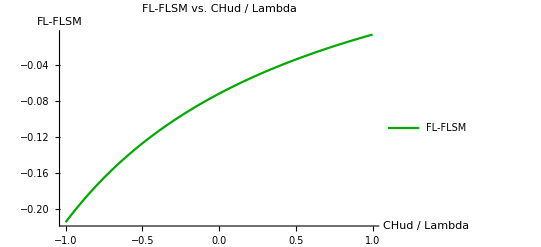

```mathematica
Plot[FL-FLSM,{CHud,-1,1},PlotStyle->{Darker[Green]},AxesLabel->{"CHud / Lambda","FL-FLSM"},PlotLabel->"FL-FLSM vs. CHud / Lambda",PlotRange->All,PlotLegends->{"FL-FLSM"}]
```

```mathematica
Clear[CHud,C3phiq,CtW,CbW]
```

```mathematica
CHud=1;
C3phiq;
CtW=1;
CbW=1;
```

```mathematica
FL
```

(6368.04 (2314.47 (8.76242×10^6+2.87783×10^6 Conjugate[C3phiq])+0.6483 (-2.25612×10^7-7.40975×10^6 Conjugate[C3phiq]+284935. (83596.5+27455.5 Conjugate[C3phiq]))))/(4.4216×10^7 (8.76242×10^6+8.11095×10^6 Conjugate[C3phiq])-0.6483 (2.15563×10^11+5.44344×10^9 (-50812.6-27455.5 Conjugate[C3phiq])+1.56645×10^11 Conjugate[C3phiq]))

```mathematica
FLSM
```

0.301225

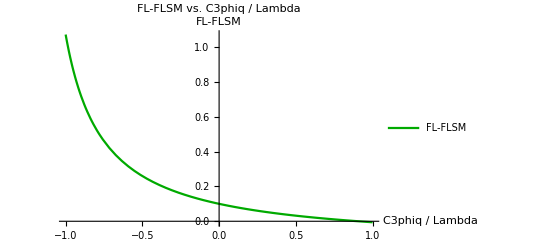

```mathematica
Plot[FL-FLSM,{C3phiq,-1,1},PlotStyle->{Darker[Green]},AxesLabel->{"C3phiq / Lambda","FL-FLSM"},PlotLabel->"FL-FLSM vs. C3phiq / Lambda",PlotRange->All,PlotLegends->{"FL-FLSM"}]
```

```mathematica
Clear[CHud,C3phiq,CtW,CbW]
```

```mathematica
CHud=1;
C3phiq=1;
CtW;
CbW=1;
```

```mathematica
FL
```

(6368.04 (2314.47 (2.87783×10^6+8.76242×10^6 CtW)+0.6483 (-7.40975×10^6-2.25612×10^7 CtW+284935. (27455.5+83596.5 CtW))))/(4.4216×10^7 (8.11095×10^6+8.76242×10^6 CtW)-0.6483 (1.56645×10^11+5.44344×10^9 (-27455.5-50812.6 CtW)+2.15563×10^11 CtW))

```mathematica
FLSM
```

0.301225

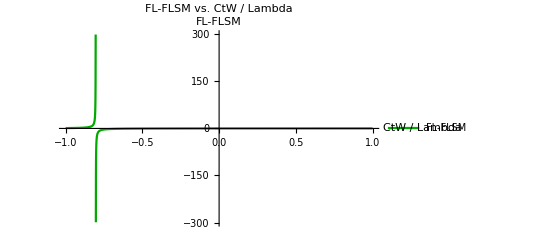

```mathematica
Plot[FL-FLSM,{CtW,-1,1},PlotStyle->{Darker[Green]},AxesLabel->{"CtW / Lambda","FL-FLSM"},PlotLabel->"FL-FLSM vs. CtW / Lambda",PlotRange->All,PlotLegends->{"FL-FLSM"}]
```

```mathematica
Clear[CHud,C3phiq,CtW,CbW]
```

```mathematica
CHud=1;
C3phiq=1;
CtW=1;
CbW;
```

```mathematica
FL
```

(6368.04 (2.04945×10^10+2.6941×10^10 Conjugate[CbW]))/(2.75965×10^14+7.46073×10^14 Conjugate[CbW])

```mathematica
FLSM
```

0.301225

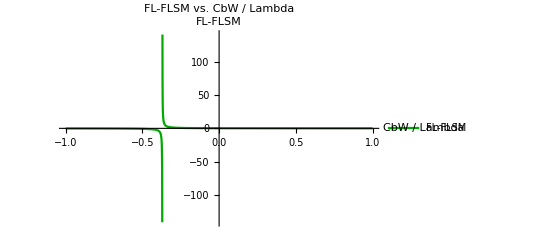

```mathematica
Plot[FL-FLSM,{CbW,-1,1},PlotStyle->{Darker[Green]},AxesLabel->{"CbW / Lambda","FL-FLSM"},PlotLabel->"FL-FLSM vs. CbW / Lambda",PlotRange->All,PlotLegends->{"FL-FLSM"}]
```

```mathematica
Clear[CHud,C3phiq,CtW,CbW]
```

```mathematica
CHud;
C3phiq;
CtW=1;
CbW=1;
```

```mathematica
FL
```

(6368.04 (2314.47 (8.76242×10^6+2.87783×10^6 Conjugate[C3phiq])+0.6483 (-2.25612×10^7-7.40975×10^6 Conjugate[C3phiq]+284935. (83596.5+27455.5 Conjugate[C3phiq]) Conjugate[CHud])))/(4.4216×10^7 (8.76242×10^6+8.11095×10^6 Conjugate[C3phiq])-0.6483 (2.15563×10^11+1.56645×10^11 Conjugate[C3phiq]+5.44344×10^9 (-50812.6-27455.5 Conjugate[C3phiq]) Conjugate[CHud]))

```mathematica
FLSM
```

0.301225

```mathematica
ContourPlot[Re[FL],{C3phiq,-1,1},{CHud,-1,1},Contours->20,ColorFunction->"ThermometerColors",PlotLegends->Automatic,FrameLabel->{"Re[C3phiq]","Re[CHud]"},PlotPoints->100]
```

-Graphics-

```mathematica
Clear[CHud,C3phiq,CtW,CbW]
```

```mathematica
CHud=1;
C3phiq=1;
CtW;
CbW;
```

```mathematica
FL
```

(6368.04 (0.6483 (-7.40975×10^6-2.25612×10^7 CtW+284935. (27455.5+83596.5 CtW))+2314.47 (2.87783×10^6+8.76242×10^6 CtW) Conjugate[CbW]))/(-0.6483 (1.56645×10^11+5.44344×10^9 (-27455.5-50812.6 CtW)+2.15563×10^11 CtW)+4.4216×10^7 (8.11095×10^6+8.76242×10^6 CtW) Conjugate[CbW])

```mathematica
FLSM
```

0.301225

```mathematica
ContourPlot[Re[FL],{CtW,-1,1},{CbW,-1,1},Contours->20,ColorFunction->"ThermometerColors",PlotLegends->Automatic,FrameLabel->{"Re[CtW]","Re[CbW]"},PlotPoints->100]
```

-Graphics-